# Compiling the reaction schema simulator to CRNs

Release version 0.1 alpha, by Erik Winfree

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022.
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

Compiling reaction schemata often won’t be possible or feasible, but there are a few special use cases of interest where the compilation gives us the speed and convenience we need to explore some interesting systems.  First, we recall the core code from ReactionSchemaSimulator.nb.

# The reaction schema simulator code

```mathematica
Protect[rxninstance,rxnschema,rxnprop,count,Symbolic];
SetAttributes[rxnschema,HoldAll];
```

```mathematica
(* do the pattern-matching and instantiate each schema as a reaction instance, if applicable, given specific reactants *)
Clear[JITReactions]
JITReactions[rxnschema[lhs_,rhs_,k_]]:=rxninstance[0,First[#],Last[#]]&/@ReplaceList[0, lhs:>{rhs,k}]
JITReactions[rxnschema[lhs_,rhs_,k_],species_]:=rxninstance[species,First[#],Last[#]]&/@ReplaceList[species, lhs:>{rhs,k}]
 (* make sure the stoichiometry-2 case works whether the pattern is simplified or not: *)
JITReactions[rxnschema[lhs_,rhs_,k_],species_,species_]:=rxninstance[2species,First[#],Last[#]]&/@Join[
ReleaseHold[ReplaceList[Hold[2species], Hold[lhs]:>{rhs,k}]],
ReleaseHold[ReplaceList[Hold[species+species], Hold[lhs]:>{rhs,k}]]]
JITReactions[rxnschema[lhs_,rhs_,k_],species1_,species2_]:=rxninstance[species1+species2,First[#],Last[#]]&/@ReplaceList[species1+species2, lhs:>{rhs,k}]
JITReactions[schemata_,reactants___]:=Flatten[JITReactions[#,reactants]&/@(schemata/.rxninstance->rxnschema)]
```

```mathematica
(* finds count-dependent propensities for all reactions that can occur in a given state *)
Clear[JITPropensities]
JITPropensities[schemata_]:=JITReactions[schemata]/. rxninstance[x_,y_,k_]:>rxnprop[x,y,k]
JITPropensities[schemata_,count[species_,count_]]:=JITReactions[schemata,species]/. rxninstance[x_,y_,k_]:>rxnprop[x,y,k*count]
JITPropensities[schemata_,count[species1_,count1_],count[species2_,count2_]]:=JITReactions[schemata,species1,species2]/. rxninstance[x_,y_,k_]:>rxnprop[x,y,k*count1*(count2-Boole[species1===species2])]
JITPropensities[schemata_,countstate_]:=Join[
Flatten[JITPropensities[schemata]],
Flatten[JITPropensities[schemata,#]&/@countstate],
Flatten[Outer[If[OrderedQ[{#1,#2}],JITPropensities[schemata,#1,#2],{}]&,countstate,countstate]]
]
```

```mathematica
(* inexplicably, Variables[] will find symbols with filled-out arguments, such as Stack1[A,C,T], but not empty ones like Stack1[] *)
SymbolicVariables[poly_]:=Variables[poly/.h_[]->Symbolic[h[]]]/.Symbolic[v_]->v
SumToCount[state_]:=count[#,Coefficient[state,#]]&/@SymbolicVariables[state]
CountToSum[countstate_]:= Plus@@(countstate /.count[s_,c_]->c*s)
SpeciesInSum[state_]:=SymbolicVariables[state]
```

```mathematica
(* for speed, avoid some redundancies by only calculating propensities for reactions involving at least one species whose count has changed *)
JITUpdatePropensities[schemata_,oldpropensities_,oldstate_,newstate_]:=Module[{changedvariables,changedcounts,unchangedcounts,unchangedpropensities,newpropensities},
changedvariables=SymbolicVariables[newstate-oldstate];
changedcounts=Cases[count[#,Coefficient[newstate,#]]&/@changedvariables,Except[count[_,0]]]; (* some of these might be zero; don't need them *)
unchangedcounts=count[#,Coefficient[newstate,#]]&/@Complement[SymbolicVariables[newstate],changedvariables]; (* none of these are zero already*)
unchangedpropensities=Cases[oldpropensities,Except[rxnprop[r_,_,_]/;ContainsAny[changedvariables,SymbolicVariables[r]]]];
newpropensities=Join[
Flatten[JITPropensities[schemata,#]&/@changedcounts],
Flatten[Outer[If[OrderedQ[{#1,#2}],JITPropensities[schemata,#1,#2],{}]&,changedcounts,changedcounts]],
Flatten[Outer[JITPropensities[schemata,#1,#2]&,changedcounts,unchangedcounts]]
];
unchangedpropensities~Join~newpropensities
]
```

```mathematica
SimulateReactionSchema[schemata_,initialstate_,tmax_]:=Module[{reactionpropensities,reaction,state=initialstate,newstate,newreactionpropensities,t=0,history},
history={{t,Expand[state]}};
reactionpropensities=JITPropensities[schemata,SumToCount[state]];
While[Length[reactionpropensities]>0 && Plus@@(Last/@reactionpropensities)>0 && t<tmax,
reaction=Take[RandomChoice[(Last/@reactionpropensities)->(reactionpropensities)],2];
newstate=Expand[state-First[reaction]+Last[reaction]];
t = t+Log[1/RandomReal[]]/(Plus@@(Last/@reactionpropensities));
AppendTo[history,{t,newstate}];
newreactionpropensities=JITUpdatePropensities[schemata,reactionpropensities,state,newstate];
(* If[Sort[JITPropensities[schemata,SumToCount[newstate]]]=!=Sort[newreactionpropensities],
Print["Updated: ",Sort[newreactionpropensities],"\nRecalculated: ",Sort[JITPropensities[schemata,SumToCount[newstate]]]];Return[]]; *)
state=newstate;reactionpropensities=newreactionpropensities;
];
history
]
```

```mathematica
DataTrace[history_,specie_]:={First[#],Coefficient[Last[#],specie]}&/@history
```

```mathematica
DataMean[history_,specie_]:=Module[{data,durations,counts},
data=DataTrace[history,specie];
durations=Differences[First/@data];
counts=Drop[Last/@data,-1];
(Plus@@(counts*durations))/(Plus@@durations)
]
```

```mathematica
DataVariance[history_,specie_]:=Module[{data,durations,counts,mean},
data=DataTrace[history,specie];
durations=Differences[First/@data];
counts=Drop[Last/@data,-1];
mean=(Plus@@(counts*durations))/(Plus@@durations);
(Plus@@((counts-mean)^2*durations))/(Plus@@durations)
]
```

# Enumerators and compilers

## Reasonably fast CRN simulation with David Soloveichik’s CRN Simulator Package.

David Soloveichik’s CRN simulator runs stochastic simulations by using Mathematica’s ability to compile functions to C; each given CRN is produced as C code and compiled, then simulated.  The source files should be placed in the same directory as this notebook.

```mathematica
SetDirectory[NotebookDirectory[]];
If[FileExistsQ["CRNSimulator.m"],Get["CRNSimulator.m"]; Print["Soloveichiks' CRN Simulator loaded..."]];
If[FileExistsQ["CRNSimulatorSSA.m"],Get["CRNSimulatorSSA.m"]; Print["Soloveichiks' CRN SSA Simulator loaded..."]];
```

Soloveichiks' CRN Simulator loaded...

Soloveichiks' CRN SSA Simulator loaded...

We also use some code that makes plotting long stochastic trajectories from CRNSimulatorSSA much faster and more convenient.

```mathematica
WeightedTrajectory[trajectory_,speciesIndex_,OptionsPattern[{Normalized->False}]]:=WeightedData[
Floor[#[[speciesIndex]]]&/@Drop[trajectory["Values"],-1],
Differences[trajectory["Times"]]/If[OptionValue[Normalized],Last[trajectory["Times"]],1]]
```

```mathematica
WeightedTrajectory[trajectory_,rsys_,speciesName_,OptionsPattern[{Normalized->False}]]:=With[{speciesIndexMap=MapThread[Rule,{SpeciesInRxnsys[rsys],Range[Length[SpeciesInRxnsys[rsys]]]}]},
WeightedTrajectory[trajectory,If[ListQ[speciesName],Replace[#,speciesIndexMap]&/@speciesName,Replace[speciesName,speciesIndexMap]],Normalized->OptionValue[Normalized]]]
```

```mathematica
PlotFormat[trajectory_,maxpoints_]:=With[{data=trajectory["Values"]},Module[{K=Length[First[data]],N=Length[data],indices},
indices=If[N<maxpoints,Range[1,N],Sort[{1,N}~Join~RandomSample[Range[2,N-1],maxpoints]]];
Table[MapThread[List,{trajectory["Times"][[indices]],data[[indices,k]]}],{k,1,K}]]]
```

```mathematica
PlotFormat[trajectory_,rsys_,formulas_,maxpoints_]:=Module[{s=SpeciesInRxnsys[rsys],calculate},
calculate=Function[{state},formulas/.MapThread[Rule,{s,state}]];
PlotFormat[TimeSeriesMap[calculate,trajectory],maxpoints]]
```

## Exhaustive enumeration of reaction schema from an initial finite set of species

In the general case, a reaction schema system may produce an infinite variety of species.  In those cases, compiling to a CRN will not be possible.  But in some cases, given a finite set of species that may be in an initial state, only a finite set of additional species can be reached even if, perhaps, the counts of the initial species may potentially be arbitrarily large.   In such cases, we can enumerate all the species that can conceivably be created, by applying reaction schemata between presently-enumerated species until nothing more is discovered.

```mathematica
Options[EnumerateReactionSchema]={MaxSpecies->1000,ReactionOrder->{0,1,2}};
EnumerateReactionSchema[schemata_,initialstate_,OptionsPattern[]]:=Module[{species,reactions,spec,spec1,spec2,react,newspecies,maxspecies,orders},
maxspecies=OptionValue[MaxSpecies];orders=OptionValue[ReactionOrder];If[IntegerQ[orders],orders={orders}];
species={};
newspecies=Union[SumToCount[initialstate]/.{count[s_,v_]:>s}];
While[newspecies=!=species && Length[newspecies]≤ maxspecies,
species=newspecies;
reactions=Union[Join[
JITReactions[schemata,0]//If[MemberQ[orders,0],#,{}]&,
Flatten[Table[JITReactions[schemata,spec],{spec,species}]]//If[MemberQ[orders,1],#,{}]&,
Flatten[Table[JITReactions[schemata,spec1,spec2],{spec1,species},{spec2,species}]]//If[MemberQ[orders,2],#,{}]&
]]/.{rxninstance->rxn};
newspecies=Union[species,Flatten[Table[SumToCount[react[[2]]]/.{count[s_,v_]:>s},{react,reactions}]]];
];
If[Length[newspecies]>maxspecies,Print["WARNING: Enumeration stopped because maximum number of species about to be exceeded.  Enumeration is incomplete."]];
reactions
]
```

Soloveichik’s CRN simulator includes the initial conditions in the reaction system definition as conc statements, so we need to be able to convert from the Reaction Schema Simulator’s conventions to the needed ones.  We might subsequently want to stick with the CRN simulator’s output format, or we might want to convert back to the Reaction Schema Simulator’s output format for comparison.

```mathematica
ToConcSSA[initialstate_]:=SumToCount[initialstate]/.{count->conc}
```

```mathematica
FromVectorSSA[crn_,statevector_]:=Plus@@MapThread[Times,{statevector,SpeciesInRxnsys[crn]}]
```

```mathematica
FromTrajectorySSA[crn_,trajectory_]:=MapThread[List,{trajectory["Times"],FromVectorSSA[crn,#]&/@trajectory["Values"]}]
```

## Simple tests from ReactionSchemaSimulator.nb

We’ll test it first on the the very simple CRN example from the basic tutorial, taking a look at data formats.  Now when we simulate it, we see that the CRN Simulator is about 160x faster here (e.g. 40 sec vs 0.25 sec for simulations that make it all the way to t=25).  Also, we can perform ODE simulations of bulk behavior, which is great.

```mathematica
Vm=50;  (* volume is V * 1.66 fL when using nM in rate constants *)
CyclicPredatorPrey={
rxninstance[R+P,2P,1/Vm],
rxninstance[P+S,2S,1/Vm],
rxninstance[S+R,2R,1/Vm]
};
```

```mathematica
schemataCPP=CyclicPredatorPrey
```

{rxninstance[P+R,2 P,1/50],rxninstance[P+S,2 S,1/50],rxninstance[R+S,2 R,1/50]}

```mathematica
initialstateCPP=100P+125R+150S
```

100 P+125 R+150 S

```mathematica
crnCPP=EnumerateReactionSchema[schemataCPP,initialstateCPP]
```

{  P+R⟶^(1/50)2 P,  P+S⟶^(1/50)2 S,  R+S⟶^(1/50)2 R}

```mathematica
ToConcSSA[initialstateCPP]
```

{conc[P,100],conc[R,125],conc[S,150]}

```mathematica
Join[crnCPP,ToConcSSA[initialstateCPP]]
```

{  P+R⟶^(1/50)2 P,  P+S⟶^(1/50)2 S,  R+S⟶^(1/50)2 R,conc[P,100],conc[R,125],conc[S,150]}

```mathematica
Timing[history=SimulateReactionSchema[schemataCPP,initialstateCPP,25];]
```

{43.2188,Null}

```mathematica
Timing[trajectory=SimulateRxnsysSSA[Join[crnCPP,ToConcSSA[initialstateCPP]],25];]
```

CCompilerDriver`CreateLibrary::cmperr: Compile error: C:\Users\User\AppData\Roaming\Mathematica\ApplicationData\CCompilerDriver\BuildFolder\user-pc-26812\Working-user-pc-26812-2828-1\compiledFunction0.c(1): fatal error C1083: Cannot open include file: 'math.h': No such file or directory

Compile::nogen: A library could not be generated from the compiled function.

CCompilerDriver`CreateLibrary::cmperr: Compile error: C:\Users\User\AppData\Roaming\Mathematica\ApplicationData\CCompilerDriver\BuildFolder\user-pc-26812\Working-user-pc-26812-2828-2\compiledFunction1.c(1): fatal error C1083: Cannot open include file: 'math.h': No such file or directory

Compile::nogen: A library could not be generated from the compiled function.

{0.453125,Null}

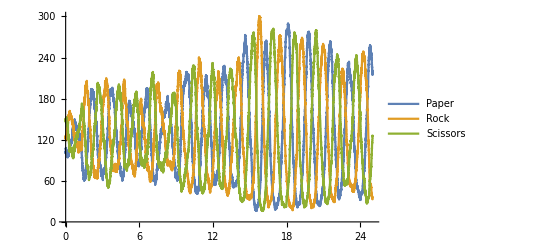

```mathematica
ListLinePlot[{DataTrace[history,P],DataTrace[history,R],DataTrace[history,S]},PlotLegends->{Paper,Rock,Scissors}]
```

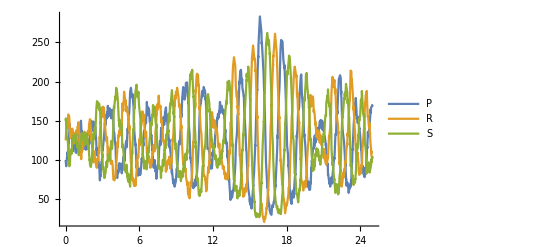

```mathematica
ListLinePlot[trajectory,PlotRange->{0,All},PlotLegends->SpeciesInRxnsys[crnCPP],MaxPlotPoints->500]
```

```mathematica
historySSA=FromTrajectorySSA[crnCPP,trajectory]; (* SSA simulation can be plotted in the same way as the original simulation, if you want. *)
```

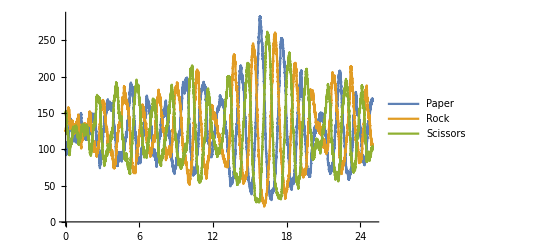

```mathematica
ListLinePlot[{DataTrace[historySSA,P],DataTrace[historySSA,R],DataTrace[historySSA,S]},PlotLegends->{Paper,Rock,Scissors}]
```

CCompilerDriver`CreateLibrary::cmperr: Compile error: C:\Users\User\AppData\Roaming\Mathematica\ApplicationData\CCompilerDriver\BuildFolder\user-pc-26812\Working-user-pc-26812-2828-3\compiledFunction2.c(1): fatal error C1083: Cannot open include file: 'math.h': No such file or directory

Compile::nogen: A library could not be generated from the compiled function.

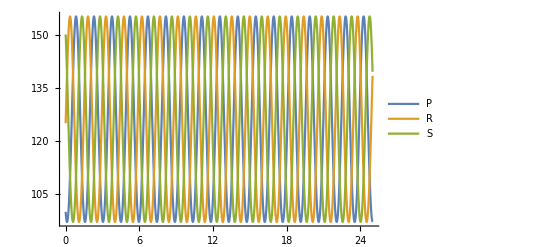

```mathematica
sol=SimulateRxnsys[Join[crnCPP,ToConcSSA[initialstateCPP]],25]; (* and now an ODE simulation too! *)
Plot[Evaluate[{P[t],R[t],S[t]}/.sol],{t,0,25},PlotRange->{0,All},PlotLegends->{P,R,S}]
```

For the binary counter CRN square-wave oscillator, the comparison is 25 seconds vs 5 seconds, which is about 5x faster.  So the speed-up will depend on the CRN and the initial state.  We also get to see clearly that the binary counter logic depends on the 0/1 nature of stochastic counts, and no oscillation appears in bulk.

```mathematica
K=8; (* number of bits in counter; N = 2^K *)
BinaryCounterOscillatorCRN=Flatten[{
Table[rxninstance[c[k]+b[k,0],b[k,1]+c[0],1],{k,0,K-1}],
Table[rxninstance[c[k]+b[k,1],b[k,0]+c[Mod[k+1,K]],1],{k,0,K-1}]
}];
```

```mathematica
schemataBCO=BinaryCounterOscillatorCRN;
initialstateBCO=c[0]+Sum[b[k,0],{k,0,K-1}];
crnBCO=EnumerateReactionSchema[schemataBCO,initialstateBCO];
```

```mathematica
Timing[history=SimulateReactionSchema[schemataBCO,initialstateBCO,10000];]
```

{25.4883,Null}

```mathematica
Timing[history=FromTrajectorySSA[crnBCO,SimulateRxnsysSSA[Join[crnBCO,ToConcSSA[initialstateBCO]],10000]];]
```

{5.46476,Null}

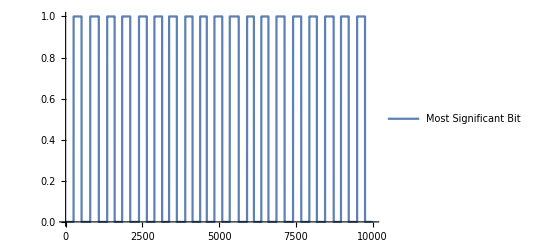

```mathematica
ListLinePlot[{DataTrace[history,b[K-1,1]]},PlotLegends->{"Most Significant Bit"}]
```

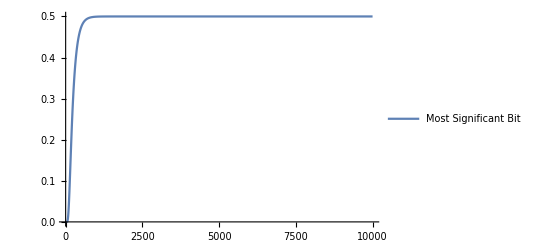

```mathematica
sol=SimulateRxnsys[Join[crnBCO,ToConcSSA[initialstateBCO]],10000]; (* sure don't work in bulk! *)
Plot[Evaluate[{b[K-1,1][t]}/.sol],{t,0,10000},PlotRange->{0,All},PlotLegends->{"Most Significant Bit"}]
```

## Non-exhaustive enumeration based on species that occur in trial simulations (non-essential)

The above hardly seem exciting, since the original system was essentially a finite CRN already... why did we even use the Reaction Schema Simulator in the first place?  Well, polymers!  But in many of the polymer systems described above, where reaction schema are essential for describing the behavior, we cannot use EnumerateReactionSchema because exhaustive enumeration cannot list out the infinite number of possible species that could potentially be reached from the initial species.  And in other cases, such as the polymer binary counter, the resulting set of species would be finite but exponentially large, making exhaustive enumeration infeasible.  However, there are also many cases where reaction schema allow us concisely represent a wide range of systems, but each system will be finite.  Genetic regulatory networks (GRNs) and PEN-DNA systems, both discussed below, are examples of such classes of systems.  We will demonstrate the substantial usefulness of SimulateReactionSchemaSSA when we explore those systems below.  Here, we’ll just demonstrate it conceptually with the abstract restriction enzyme system from above.  Alas, this demonstration is weak, as Soloveichik’s simulator is very slow compiling and running large CRNs, and this system has over 1000 reactions.  There is an (almost) plug-and-play compatible CRNSimulatorSSA5 that works well for CRNs containing up to 40,000 reactions, available here: https://www.dna.caltech.edu/SupplementaryMaterial/CRNSAT/ .  That said, the GRN and PEN-DNA examples will be compelling even without it.

```mathematica
(* also from ReactionSchemaSimulator.nb *)
RestrictionPRN={
rxnschema[R[i_]+DNA[x___,S[i_],y___],R[i]+DNA[x,Sdown[i]]+DNA[Sup[i],y],1.0], (* restrict *)
rxnschema[DNA[x___,Sdown[i_]]+DNA[Sup[i_],y___],DNA[x,s[i],y],1.0], (* associate *)
rxnschema[DNA[x___,s[i_],y___],DNA[x,Sdown[i]]+DNA[Sup[i],y],1.0], (* dissociate *)
rxnschema[L[i_]+DNA[x___,s[i_],y___],L[i]+DNA[x,S[i],y],1.0] (* ligate *)
};
```

```mathematica
schemataRPRN=RestrictionPRN;
initialstateRPRN=R[1]+R[2]+R[3]+L[1]+L[2]+L[3]+10 DNA[A,S[1],B,S[2],C,S[3],D]+10DNA[a,S[1],b,S[2],c,S[3],d];
```

```mathematica
crnRPRN=EnumerateReactionSchema[schemataRPRN,initialstateRPRN];Length[crnRPRN]
```

1072

```mathematica
Timing[history=SimulateReactionSchemaSSA[schemataRPRN,initialstateRPRN,20];] (* scramble them! originally took 96 seconds *)
```

{92.9385,Null}

```mathematica
Timing[history=SimulateReactionSchemaSSA[schemataRPRN,Last[Last[history]/.R[_]->0],10]; ] (* ligate them! originally took 2.3 seconds *)
```

{27.0439,Null}

```mathematica
Last[history]
```

{8.72607,2 DNA[a,S[1],b,S[2],c,S[3],d]+DNA[a,S[1],b,S[2],c,S[3],D]+2 DNA[a,S[1],b,S[2],C,S[3],d]+2 DNA[a,S[1],b,S[2],C,S[3],D]+DNA[a,S[1],B,S[2],c,S[3],d]+DNA[a,S[1],B,S[2],c,S[3],D]+DNA[a,S[1],B,S[2],C,S[3],D]+DNA[A,S[1],b,S[2],c,S[3],D]+DNA[A,S[1],b,S[2],C,S[3],d]+DNA[A,S[1],b,S[2],C,S[3],D]+2 DNA[A,S[1],B,S[2],c,S[3],d]+2 DNA[A,S[1],B,S[2],c,S[3],D]+2 DNA[A,S[1],B,S[2],C,S[3],d]+DNA[A,S[1],B,S[2],C,S[3],D]+L[1]+L[2]+L[3]}

Can we perform fast simulation even in systems where exhaustive enumeration is not possible?  One approach to this problem is to perform a slow schema simulation for a while, collect the set of species that have come up so far, build a CRN using those species, and then perform a fast simulation for the rest of the time.  Since exhaustive enumeration was by assumption not possible, that means that this CRN will have some species that could react according to the schema, but for which the reaction was not included in the CRN.   We will replace such reactions by a “stub” where the reactants and rate constant are as usual, but the product is catalytic production of the new species MISSINGREACTION.  There are cases where such “stub” reactions will (provably) never occur, such as when CRN reachability from the given initial state will never allow both species to coexist. (For example, with 100 initial monomers and mass-conserving reactions, no subsequent polymer will ever grow to length greater than 100, even though the CRN will have the monomer species and the length-100 polymer species and the reaction schemata include a reaction between the monomer and the length-100 polymer.)  In other cases, such “stub” reactions simply may be very rare, so most fast simulations will be valid, and we can test whether they were in fact valid by looking for the MISSINGREACTION species (and even determine when the first such case occurred).

```mathematica
Clear[MISSINGREACTION];
Options[ObservableReactionSchema]={MinUniRate->10^-6,MinBiRate->10^-9};
ObservableReactionSchema[schemata_,initialstate_, tmax_,OptionsPattern[]]:=Module[{history,species,reactions,spec,spec1,spec2,react,prod,k},
history=SimulateReactionSchema[schemata,initialstate,tmax];
If[First[Last[history]]>tmax,history=Drop[history,-1]]; (* unless system halts first, last event is *past* tmax, may be freaky *)
species=Union[SumToCount[Plus@@(Last/@history)]/.{count[s_,v_]:>s}];
reactions=Union[Join[
JITReactions[schemata,0],
Flatten[Table[JITReactions[schemata,spec],{spec,species}]],
Flatten[Table[JITReactions[schemata,spec1,spec2],{spec1,species},{spec2,species}]]
]]/.{rxninstance->rxn};
reactions=Cases[reactions,rxn[Except[_Plus],_,k_/;k≥OptionValue[MinUniRate]]|rxn[_Plus,_,k_/;k≥OptionValue[MinBiRate]]];
reactions/.{rxn[react_,prod_,k_]/;!ContainsAll[species,SumToCount[prod]/.{count[s_,v_]:>s}]:> rxn[react,react+MISSINGREACTION,k]}
]
```

Now we will speed up a slow polymer oscillator.  A little bit, maybe a factor of 2, depending.   Even if this isn’t so effective, it does illustrate a few points.  First, one might not need to simulate the specific system of interest in order to visit enough species for to build an adequate CRN; perhaps a smaller initial state is enough.  Second, polymer systems and other combinatorial systems often end up having a large number of distinct species, and in this case the Soloveichik simulator will be slow anyway.

```mathematica
(* also from ReactionSchemaSimulator.nb *)
SustainedPolymerRockPaperScissors={
rxnschema[R[0]+P[n_?(#>0&)],R[0]+P[n-1]+S,1],
rxnschema[S+S[n_],S[n+1],1],
rxnschema[P[0]+S[n_?(#>0&)],P[0]+S[n-1]+R,1],
rxnschema[R+R[n_],R[n+1],1],
rxnschema[S[0]+R[n_?(#>0&)],S[0]+R[n-1]+P,1],
rxnschema[P+P[n_],P[n+1],1],
rxnschema[R[0]+R[n_?(#>0&)],R[0]+R[n-1]+S,1],
rxnschema[P[0]+P[n_?(#>0&)],P[0]+P[n-1]+R,1],
rxnschema[S[0]+S[n_?(#>0&)],S[0]+S[n-1]+P,1]
};
```

```mathematica
Timing[history=SimulateReactionSchema[SustainedPolymerRockPaperScissors,5R[100]+5P[0]+5S[0],1000];]
```

{557.537,Null}

```mathematica
Timing[history=SimulateReactionSchema[SustainedPolymerRockPaperScissors,5R[100]+5P[0]+5S[0],100];]
```

{16.5133,Null}

```mathematica
schemataSPRPS=SustainedPolymerRockPaperScissors;
initialstateSPRPS=5R[100]+5P[0]+5S[0];
```

```mathematica
(* use a smaller, faster initial state that nonetheless covers the needed reactions *)Timing[crnSPRPS=ObservableReactionSchema[schemataSPRPS,3R[125]+3P[0]+3S[0],100];]
```

{16.9641,Null}

```mathematica
Length[crnSPRPS]
```

1101

```mathematica
Length[Cases[crnSPRPS,rxn[_,MISSINGREACTION|(___+MISSINGREACTION),_]]]
```

3

```mathematica
Cases[crnSPRPS,rxn[_,MISSINGREACTION|(___+MISSINGREACTION),_]]
```

{  P+P[122]⟶^1MISSINGREACTION+P+P[122],  R+R[126]⟶^1MISSINGREACTION+R+R[126],  S+S[118]⟶^1MISSINGREACTION+S+S[118]}

```mathematica
Timing[history=FromTrajectorySSA[crnSPRPS,SimulateRxnsysSSA[Join[crnSPRPS,ToConcSSA[initialstateSPRPS]],100]];]
```

{136.59,Null}

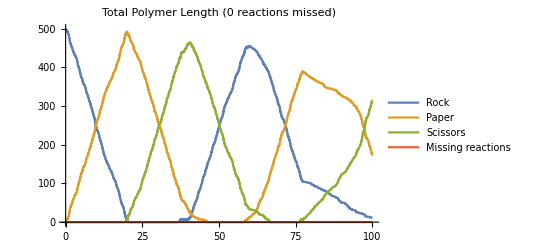

```mathematica
ListLinePlot[{
history/.{m_,state_}:>{m,state//.{R[n_]:> n, P[n_]:>0,S[n_]:>0,R->1,P->0,S->0,MISSINGREACTION->0}},
history/.{m_,state_}:>{m,state//.{R[n_]:> 0, P[n_]:>n,S[n_]:>0,R->0,P->1,S->0,MISSINGREACTION->0}},
history/.{m_,state_}:>{m,state//.{R[n_]:> 0, P[n_]:>0,S[n_]:>n,R->0,P->0,S->1,MISSINGREACTION->0}},
history/.{m_,state_}:>{m,state//.{R[n_]:> 0, P[n_]:>0,S[n_]:>0,R->0,P->0,S->0,MISSINGREACTION->1}}
},PlotLegends->{Rock,Paper,Scissors,"Missing reactions"},PlotLabel->("Total Polymer Length ("<>ToString[Last[Last[history]]//.{R[n_]:> 0, P[n_]:>0,S[n_]:>0,R->0,P->0,S->0,MISSINGREACTION->1}]<>" reactions missed)")]
```

## Convenience functions

Here’s code to automate this kind of speed-up.  There is a concern about species names.  Soloviechik’s CRN simulator works fine with X[i,j] but is not guaranteed to work with X[i][j], which in my hands works for SSA simulations but crashes the ODE simulator.  I am not sure if there are other classes of problematic species names.   Since the Reaction Schema Simulator is intended to allow species to be represented as arbitrary “inert” expressions (i.e. no pre-defined symbols or symbols with rules associated with them), it makes sense to take precautions on the safe side.  We will replace each species expression by a numbered species symbol, e.g. “species1”, “species2”, etc., which better not already be defined.   There can be considerable overhead to all these transformations, especially the final FromTrajectorySSA conversion to the reaction schema simulator’s history of algebraic states -- so if you care about speed more than convenience, you may want to do it step by step yourself to avoid unnecessary transformations, or use the SSA trajectory direction via the options setting Trajectory.

By default, the CRN is enumerated exhaustively from the reaction schemata and the initial state; this is the CRN → Enumerate option.  When the reaction schemata yield a combinatorial explosion of reaction instances, yet in practice simulation only encounters a small subset of species, the CRN → Observable option performs a just-in-time reaction schema simulation up to 1% of tmax and collates reactions involving species encountered up to that point, then re-runs the simulation from scratch using the fast CRN simulator.  The option ObservationFactor can be used to change the 1% figure.

```mathematica
ClearAll[SimulateReactionSchemaCompiled,SimulateReactionSchemaSSA,SimulateReactionSchemaBulk];

SimulateReactionSchemaCompiled::CRN="The CRN option must be Enumerate or Observable or a list of reactions.";
SimulateReactionSchemaCompiled::Method="The Method option must be SSA or Bulk.";
Options[SimulateReactionSchemaCompiled]={"Method"->"SSA","Trajectory"->False,"CRN"->"Enumerate","ObservationFactor"->0.01,"Watch"->True};
SimulateReactionSchemaCompiled[schemata_,initialstate_,tmax_,OptionsPattern[]]:=Module[{crn,species,numberedcrn,numberedspecies,tonumbers,fromnumbers,trajectory,solution},
crn=Switch[OptionValue["CRN"],
"Enumerate"|Enumerate,PrintTemporary["exhaustively enumerating CRN"];EnumerateReactionSchema[schemata,initialstate],
"Observable"|Observable,PrintTemporary["observing reaction schema simulation"];ObservableReactionSchema[schemata,initialstate,tmax OptionValue["ObservationFactor"]],
{(_rxn|_conc)...},If[OptionsValue["Watch"],PrintTemporary["using user-supplied CRN"]];OptionValue["CRN"],
_,Message[SimulateReactionSchemaCompiled::CRN]
];
species=Union[SpeciesInRxnsys[crn],ToConcSSA[initialstate]/.{conc[species_,_]:>species}];
numberedspecies=Table[ToExpression["species"<>ToString[i]],{i,1,Length[species]}];
tonumbers=MapThread[Rule,{species,numberedspecies}];fromnumbers=MapThread[Rule,{numberedspecies,species}];
numberedcrn=Join[crn/.tonumbers,ToConcSSA[initialstate]/.tonumbers];
If[OptionsValue["Watch"],PrintTemporary["numbered crn built"]];
Switch[OptionValue["Method"],
"SSA"|SSA,
	trajectory=SimulateRxnsysSSA[numberedcrn,tmax]; If[OptionsValue["Watch"],PrintTemporary["simulation done"]];
	If[OptionValue["Trajectory"],
	{trajectory,MapThread[Rule,{SpeciesInRxnsys[numberedcrn]/.fromnumbers,Range[Length[species]]}]},
	FromTrajectorySSA[numberedcrn,trajectory]/.fromnumbers ],
"Bulk"|Bulk,
	solution=SimulateRxnsys[numberedcrn,tmax];If[OptionsValue["Watch"],PrintTemporary["simulation done"]];
	solution/.fromnumbers,
_,Message[SimulateReactionSchemaCompiled::Method]
]
]

SimulateReactionSchemaSSA[schemata_,initialstate_,tmax_,opts:OptionsPattern[SimulateReactionSchemaCompiled]]:=
SimulateReactionSchemaCompiled[schemata,initialstate,tmax,"Method"->"SSA",opts]

SimulateReactionSchemaBulk[schemata_,initialstate_,tmax_,opts:OptionsPattern[SimulateReactionSchemaCompiled]]:=
SimulateReactionSchemaCompiled[schemata,initialstate,tmax,"Method"->"Bulk",opts]

FromVectorSSA[crn_,statevector_,species2numbers_]:=Plus@@MapThread[Times,{statevector[[SpeciesInRxnsys[crn]/.species2numbers]],SpeciesInRxnsys[crn]}]
FromTrajectorySSA[crn_,trajectory_,species2numbers_]:=MapThread[List,{trajectory["Times"],FromVectorSSA[crn,#,species2numbers]&/@trajectory["Values"]}]
```

```mathematica
Timing[history=SimulateReactionSchemaSSA[schemataCPP,initialstateCPP,25];]
```

{3.83099,Null}

```mathematica
Timing[history=SimulateReactionSchemaSSA[schemataBCO,initialstateBCO,10000];]
```

{6.11584,Null}

```mathematica
sol=SimulateReactionSchemaBulk[schemataCPP,initialstateCPP,25];
Plot[Evaluate[{P[t],R[t],S[t]}/.sol],{t,0,25},PlotRange->{0,All},PlotLegends->{P,R,S}]
```

-Graphics-

# Exploring the Central Dogma of Molecular Biology

## Genetic Regulatory Networks

These  six reaction schemata are sufficient for basic genetic regulatory network models with inhibitory repressor proteins and arbitrary network topology.  The Genome[] species represents the genome as a single molecule, containing a sequence of elements (and possibly whatever binds to them).  Transcription by RNA polymerase (RNAP) occurs whenever a Promoter[] element directly precedes a Gene[] element.  mRNA is degraded by a ribonuclease (RNase) and translated into protein by a ribosome (Ribosome), and the protein in turn is degraded by a protease (Protease).   Cell growth and the associated dilution is not modeled.  Proteins bind to their corresponding Promoter[] element, transforming it into an inactive Bound[] element.  Genes, mRNA, and proteins are by default numbered, although you could label them in any way you want so long as a matching rate constant formula is provided.

Note that default reaction rate constants are provided; you can override them with a direct assignment, e.g. ktx[3]=0.05 to make promoter 3 ten times stronger than the default.  The “i_Integer” pattern matching ensures that the default isn’t applied while symbol i is not yet bound to a value during pattern matching for the schema.

Also note that these simulations are slow... so slow that you might not want to run them yourself... indicating a need for a compiler for reaction schema, much like the compiler already used for classical CRNs.  For another time... (We informally explore compiling at the very end, which yields a roughly 2000x speed-up, but we don’t develop the code into a reliable general purpose method -- it only works for cases where there are a small, finite number of species.)

It’s worth clarifying that if you actually want to study genetic regulatory networks, the Reaction Schema Simulator is not the approach you’d want to use, because of speed (for now).  The point of these examples is just (a) to illustrate how a finite number of general reaction mechanisms can capture the infinite possibilities inherent in a polymer-modifying enzyme system, dependent upon just the initial condition consisting of a single-molecule genome, and (b) to have some fun thinking about signal restoration via nonlinear input/output curves.

```mathematica
GRNschemata = {
rxnschema[Genome[a___,Promoter[i_],Gene[j_],b___]+RNAP,Genome[a,Promoter[i],Gene[j],b]+RNAP+mRNA[j],ktx[i]],
rxnschema[mRNA[j_]+RNase,RNase,krd[j]],
rxnschema[mRNA[j_]+Ribosome,mRNA[j]+Ribosome+Protein[j],ktl[j]],
rxnschema[Protein[j_]+Protease,Protease,kpd[j]],
rxnschema[Genome[a___,Promoter[i_],b___]+Protein[i_],Genome[a,Bound[i],b],kbp[i]],
rxnschema[Genome[a___,Bound[i_],b___],Genome[a,Promoter[i],b]+Protein[i],kup[i]]
};
```

```mathematica
DefaultGRNrates:=Module[{},
Clear[ktx,krd,ktl,kpd,kbp,kup];
ktx[i_Integer]:=0.005; (* transcript rate constant in volume s.t. 1 molecule = 1 nM, i.e. bacterial scale *)
krd[i_Integer]:=0.01; (* mRNA degradation rate *)
ktl[i_Integer]:=0.0005; (* translation rate constant *)
kpd[i_Integer]:=0.01; (* protein degradation rate *)
kbp[i_Integer]:=0.1; (* protein regulator binding to promoter site *)
kup[i_Integer]:=1.0; (* protein regulator unbinding *)
]
DefaultGRNrates
```

For the “plausible” enzyme concentrations below and rate constants above, mRNA production and degradation are balanced when 50 = 10 #mRNA, and protein production and degradation are balanced when 25 #mRNA = 5 #protein.  Thus, we expect about 5 mRNA and 25 protein copies per cell, on average.

```mathematica
initialstate=Genome[Promoter[1],Gene[2]] + 10000RNAP+50000Ribosome+1000RNase+500Protease
```

500 Protease+50000 Ribosome+10000 RNAP+1000 RNase+Genome[Promoter[1],Gene[2]]

```mathematica
Timing[history=SimulateReactionSchema[GRNschemata,initialstate,50];] (* this will take a little while *)
```

{45.4544,Null}

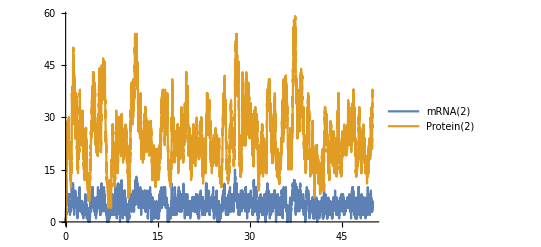

```mathematica
ListLinePlot[{DataTrace[history,mRNA[2]],DataTrace[history,Protein[2]]},PlotLegends->{mRNA[2],Protein[2]}]
```

```mathematica
{DataMean[history,mRNA[2]],DataMean[history,Protein[2]]}
```

{4.86846,24.1459}

```mathematica
{DataVariance[history,mRNA[2]],DataVariance[history,Protein[2]]}
```

{5.17016,74.8662}

```mathematica
Timing[history=SimulateReactionSchemaSSA[GRNschemata,initialstate,500];] (* 10 times more simulation in less time using compiled CRN SSA *)
```

{31.5915,Null}

```mathematica
ListLinePlot[{DataTrace[history,mRNA[2]],DataTrace[history,Protein[2]]},PlotLegends->{mRNA[2],Protein[2]}]
```

-Graphics-

Because Mathematica looks for directly assigned values before applying rules, assigning specific values for rate constants for specific promoters or genes can be done easily, with the default values filled in by the rules above.  Here we make the transcription rate 10x higher and the translation rate 10x lower.  So the mean protein level is the same, but the variability is less.  Just remember to clear the specific values before constructing a new network.

```mathematica
ktx[1]=0.05; ktl[2]=0.00005;
```

```mathematica
Timing[history=SimulateReactionSchemaSSA[GRNschemata,initialstate,50];]
```

{11.9409,Null}

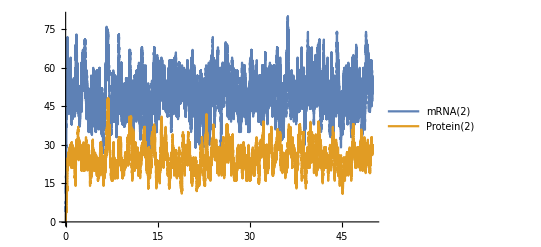

```mathematica
ListLinePlot[{DataTrace[history,mRNA[2]],DataTrace[history,Protein[2]]},PlotLegends->{mRNA[2],Protein[2]}]
```

```mathematica
{DataMean[history,mRNA[2]],DataMean[history,Protein[2]]}
```

{50.0094,24.9282}

```mathematica
{DataVariance[history,mRNA[2]],DataVariance[history,Protein[2]]}
```

{57.2048,28.3084}

It can be insightful to examine the quantitative “transfer function” for repression in this model.  So we build a genome where Protein[1] controls the level of Protein[2].  Most insightful would be to compute the mean and variance analytically, but here we simply examine it by simulation with a single data point per input protein level --  resulting in a noisy curve.

```mathematica
DefaultGRNrates
```

```mathematica
Timing[IO=Table[
initialstate=Genome[Promoter[1],Gene[2]] + 10000RNAP+50000Ribosome+1000RNase+500Protease+initialcount Protein[1];
kpd[1]=0; (* protein 1 will be at count forever *)
history=SimulateReactionSchemaSSA[GRNschemata,initialstate,100];
PrintTemporary["Simulation for input protein count ",initialcount," completed."];
{initialcount, DataMean[history,Protein[2]]},
{initialcount,0,100}
];]  (* without the compilation for CRN SSA, this took about 5000 seconds, now it's under 200, i.e. 25x faster -- revise status.  really true? -- *)
```

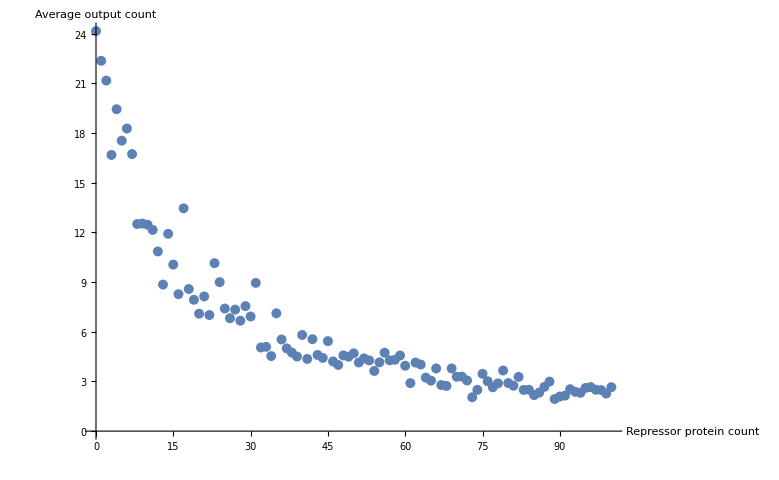

```mathematica
ListPlot[IO,AxesLabel->{"Repressor protein count","Average output count"},PlotRange->All]
```

Now we can make a network -- one of the simplest is a ring of repressors inspired by Elowitz’s Repressilator (Elowitz & Leibler, Nature, 2000).

```mathematica
DefaultGRNrates
```

```mathematica
initialstate=Genome[Promoter[1],Gene[2],Promoter[2],Gene[3],Promoter[3],Gene[1]] + 10000RNAP+50000Ribosome+1000RNase+500Protease
```

500 Protease+50000 Ribosome+10000 RNAP+1000 RNase+Genome[Promoter[1],Gene[2],Promoter[2],Gene[3],Promoter[3],Gene[1]]

```mathematica
Timing[history=SimulateReactionSchema[GRNschemata,initialstate,30];] (* this will take a few minutes *)
```

{58.7944,Null}

```mathematica
Timing[history=SimulateReactionSchemaSSA[GRNschemata,initialstate,30];] (* this will do the same job but take just a few seconds *)
```

{20.5091,Null}

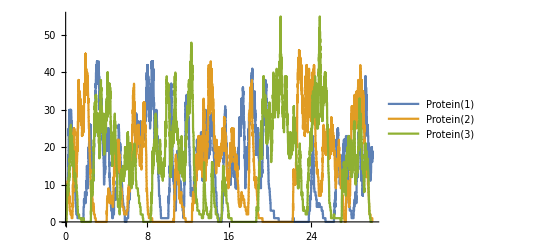

```mathematica
ListLinePlot[{DataTrace[history,Protein[1]],DataTrace[history,Protein[2]],DataTrace[history,Protein[3]]},PlotLegends->{Protein[1],Protein[2],Protein[3]}]
```

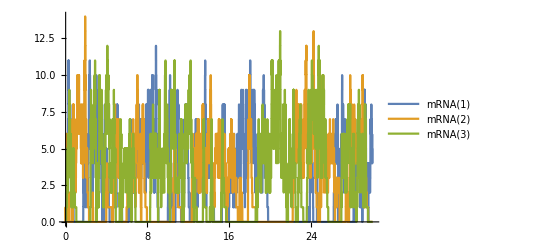

```mathematica
ListLinePlot[{DataTrace[history,mRNA[1]],DataTrace[history,mRNA[2]],DataTrace[history,mRNA[3]]},PlotLegends->{mRNA[1],mRNA[2],mRNA[3]}]
```

```mathematica
With[{f1=Interpolation[DataTrace[history,Protein[1]],InterpolationOrder->1],
f2=Interpolation[DataTrace[history,Protein[2]],InterpolationOrder->1],
f3=Interpolation[DataTrace[history,Protein[3]],InterpolationOrder->1]},
ParametricPlot3D[{f1[t],f2[t],f3[t]}, {t,0,30},ColorFunction->Function[{x,y,z,t},Hue[t/30]],ColorFunctionScaling->False]]
```

-Graphics3D-

Those are fluctuations but it would be hard to call them oscillations -- it’s hard to see a defined cycle of flow.  Discernible oscillations in a ring oscillator benefits from some sigmoidal nonlinearity in the repression function, which is not provided by direct binding.  Two known mechanisms for sigmoidal nonlinearity are dimerization of the repressor (with only the dimer being effective) and titration by competitive dimerization, as will be explored below.  These mechanisms are also sufficient for obtaining a digital abstraction, if you want to build Boolean circuits.

Below, we augment the GRN schemata to include dimerization, thus requiring a few more rate constants.  Many many biologically relevant mechanisms are still absent, most prominently protein regulators that activate transcription.  But the mechanisms below suffice for our purposes.

```mathematica
Clear[Dimers]; (* don't want rules below to get hard-coded, in case Dimers is already defined *)
GRNschemataDimers = {
rxnschema[Genome[a___,Promoter[i_],Gene[j_],b___]+RNAP,Genome[a,Promoter[i],Gene[j],b]+RNAP+mRNA[j],ktx[i]],
rxnschema[mRNA[j_]+RNase,RNase,krd[j]],
rxnschema[mRNA[j_]+Ribosome,mRNA[j]+Ribosome+Protein[j],ktl[j]],
rxnschema[Protein[j_]+Protease,Protease,kpd[j]],
rxnschema[Genome[a___,Promoter[i_],b___]+Protein[i_],Genome[a,Bound[i],b],kbp[i]],
rxnschema[Genome[a___,Bound[i_],b___],Genome[a,Promoter[i],b]+Protein[i],kup[i]],
rxnschema[Protein[i_]+Protein[j_]/;MemberQ[Dimers,{i,j}],Dimer[i,j],kbd[i,j]],
rxnschema[Dimer[i_,j_],Protein[i]+Protein[j],kud[i,j]],
rxnschema[Dimer[i_,j_]+Protease,Protease,kdd[i,j]],
rxnschema[Genome[a___,Promoter[i_],b___]+Dimer[i_,i_],Genome[a,DimerBound[i],b],kbd[i]],
rxnschema[Genome[a___,DimerBound[i_],b___],Genome[a,Promoter[i],b]+Dimer[i,i],kud[i]]
};
DefaultGRNratesWithDimers:=Module[{},
Dimers={};  (* only pairs listed here are able to dimerize *)
Clear[ktx,krd,ktl,kpd,kbp,kup];
ktx[i_Integer]:=0.005; (* transcript rate constant in volume s.t. 1 molecule = 1 nM, i.e. bacterial scale *)
krd[i_Integer]:=0.01; (* mRNA degradation rate *)
ktl[i_Integer]:=0.0005; (* translation rate constant *)
kpd[i_Integer]:=0.01; (* protein degradation rate *)
kbp[i_Integer]:=0.1; (* protein regulator binding to promoter site *)
kup[i_Integer]:=1.0; (* protein regulator unbinding *)
Clear[kdd,kbd,kud];
kdd[i_Integer,j_Integer]:=0.01; (* protein (hetero/homo)dimer degradation rate *)
kbd[i_Integer,j_Integer]:=0.1; (* protein (hetero/homo)dimer reference binding rate for forming dimer; see note below *)
kud[i_Integer,j_Integer]:=1.0; (* protein (hetero/homo)dimer unbinding rate for dimer falling apart *)
kbd[i_Integer]:=0.1; (* protein homodimer binding rate to its promoter *)
kud[i_Integer]:=1.0; (* protein homodimer unbinding rate from its promoter *)
]
DefaultGRNratesWithDimers
```

All else being equal physically and chemically, homodimers should have half the net dimerization rate as heterodimers.  (Suppose A0 and A1 are the same homodimerizing molecule, except that A1 is radiolabeled and thus distinguishable.  So 2 A0 →^k D00 and 2 A1 →^k D11 must have the same rate constant; then what is the rate constant for A0+A1 →^k' D01 ?   If we ignore the radiolabel, we just have 2 A →^k D, and with [A] = 2 c we have a total rate of 4 k c^2 for producing dimer.  Paying attention to the radiolabel and with [A0]=c and [A1]=c we have a total rate of (k c^2)+(k c^2)+(k' c^2) for producing dimer of any flavor.  These must match, so k'=2k.)  

But as can be seen from the test below, with the pattern-matching for the dimerization subcase of using the rules above, the 2 ways of matching in the dimer case yields a homodimer net rate that is twice the heterodimer rate.  If this is not what you want, then you would need to put conditions on the matching rules, or in this case, simply add a special case for kbd[i,i].

```mathematica
Dimers={{1,1},{1,2}};
JITPropensities[GRNschemataDimers,SumToCount[10Dimer[1,1]+10Dimer[1,2]+100Protein[1]+100Protein[2]]]//Column
```

rxnprop[Dimer[1,1],2 Protein[1],10.]
rxnprop[Dimer[1,2],Protein[1]+Protein[2],10.]
rxnprop[2 Protein[1],Dimer[1,1],990.]
rxnprop[2 Protein[1],Dimer[1,1],990.]
rxnprop[Protein[1]+Protein[2],Dimer[1,2],1000.]

Although slow, it is also insightful to examine the quantitative “transfer function” for repression by dimers in this model.  

I’m including here -- commented out -- how the calculation was done prior to speed-ups.  Computing the IO table took 12000 seconds for raw SimulateReactionSchema, 600 for SimulateReactionSchemaSSA with history, 80 for SimulateReactionSchemaSSA with trajectories.  The trajectories format is explaineed a little farther below.

```mathematica
Timing[IO=Table[
initialstate=Genome[Promoter[1],Gene[2]] + 10000RNAP+50000Ribosome+1000RNase+500Protease+initialcount Protein[1];
Dimers={{1,1}};
kpd[1]=0; kdd[1,1]=0; (* protein 1 (in monomer or dimer form) don't degrade *)
kbp[1]=0; (* monomer form of protein 1 does not bind to the promoter *)
ktx[1]=0.020; (* increase promoter strength to target average 20 mRNA thus average 100 protein when ON *)
kud[1,1]=100; (* weaken dimer so that concentration tracks square of monomer without saturating *)
kbd[1]=1; (* dimer binds strongly; 10 molecules is enough to significantly repress *)
(* history=SimulateReactionSchema[GRNschemataDimers,initialstate,100]; *)
(* history=SimulateReactionSchemaSSA[GRNschemataDimers,initialstate,100]; *)
{trajectory,species2numbers}=SimulateReactionSchemaSSA[GRNschemataDimers,initialstate,100,Trajectory->True]; 
PrintTemporary["Simulation for input protein count ",initialcount," completed."];
(* {initialcount, DataMean[history,Protein[2]]}, *)
{initialcount, Mean[WeightedTrajectory[trajectory,Protein[2]/.species2numbers]]},
{initialcount,0,100,2}
];]
```

{86.0714,Null}

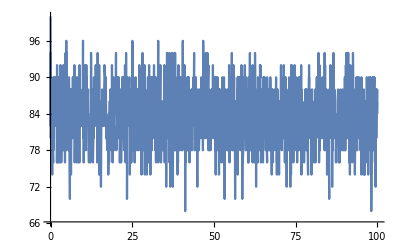
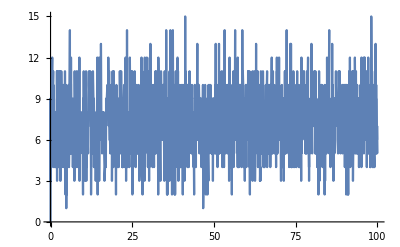
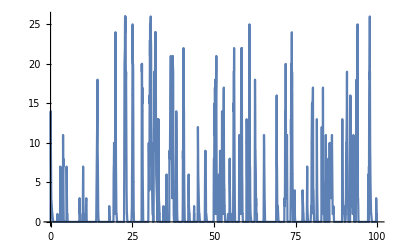
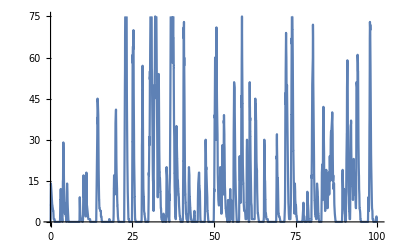

```mathematica
With[{trajlists=PlotFormat[trajectory,2000]},
{ListLinePlot[trajlists[[Protein[1]/.species2numbers]]],ListLinePlot[trajlists[[Dimer[1,1]/.species2numbers]]],
ListLinePlot[trajlists[[mRNA[2]/.species2numbers]]],ListLinePlot[trajlists[[Protein[2]/.species2numbers]]]}]
```

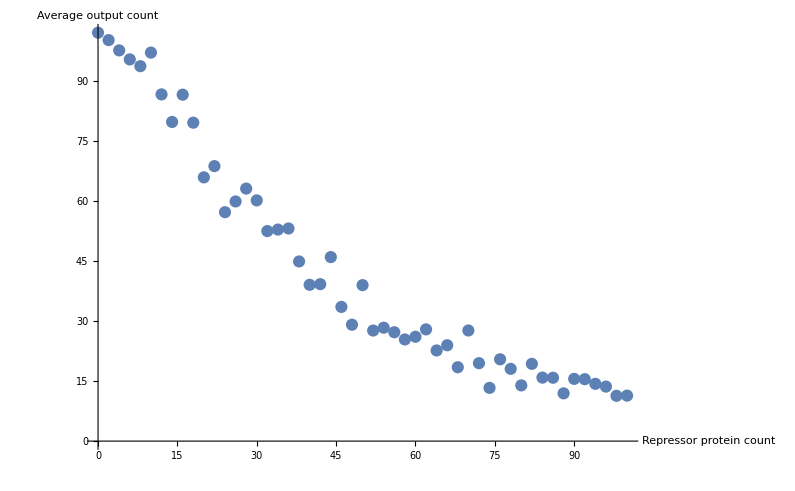

```mathematica
ListPlot[IO,AxesLabel->{"Repressor protein count","Average output count"},PlotRange->All]
```

Now we see a reasonable sigmoid(ish) curve, although, perhaps surprisingly, the output mRNA and protein are surprisingly “bursty”.  If we think this is unreasonable, we could go back and adjust the default rate constants, but we won’t.  Instead, we will go ahead and create a more realistic version of the Repressilator, using proteins that dimerize.

```mathematica
DefaultGRNratesWithDimers;
initialstate=Genome[Promoter[1],Gene[2],Promoter[2],Gene[3],Promoter[3],Gene[1]] + 10000RNAP+50000Ribosome+1000RNase+500Protease;
Dimers={{1,1},{2,2},{3,3}}; (* each protein dimerizes *)
kbp[i_Integer]:=0; (* non-dimerized protein doesn't bind *)
ktx[i_Integer]:=0.020; (* increase promoter strength to target average 20 mRNA thus average 100 protein when ON *)
kud[i_Integer,j_Integer]:=100; (* weaken dimer so that concentration tracks square of monomer without saturating *)
kbd[i_Integer]:=1; (* dimer binds strongly; 10 molecules is enough to significantly repress *)
(* note that to replace pattern-matching defaults, the same patterns must be used -- otherwise, Mathematica keeps both and which will match first depends on the order they are tried *)
```

```mathematica
Timing[history=SimulateReactionSchemaSSA[GRNschemataDimers,initialstate,30];]
```

{431.426,Null}

```mathematica
ListLinePlot[{DataTrace[history,Protein[1]],DataTrace[history,Protein[2]],DataTrace[history,Protein[3]]},PlotLegends->{Protein[1],Protein[2],Protein[3]}]
```

-Graphics-

```mathematica
ListLinePlot[{DataTrace[history,mRNA[1]],DataTrace[history,mRNA[2]],DataTrace[history,mRNA[3]]},PlotLegends->{mRNA[1],mRNA[2],mRNA[3]}]
```

-Graphics-

```mathematica
With[{f1=Interpolation[DataTrace[history,Protein[1]],InterpolationOrder->1],
f2=Interpolation[DataTrace[history,Protein[2]],InterpolationOrder->1],
f3=Interpolation[DataTrace[history,Protein[3]],InterpolationOrder->1]},
ParametricPlot3D[{f1[t],f2[t],f3[t]}, {t,0,30},ColorFunction->Function[{x,y,z,t},Hue[t/30]],ColorFunctionScaling->False]]
```

-Graphics3D-

It turns out that most of the time in the above simulation run is not taken by the SSA simulation itself, nor the enumeration and construction of the CRN from the reaction schemata, but rather by the menial task of converting from the SSA’s output format to the reaction schema simulator’s format.  The SSA simulator’s output is compact and numerical: just the time stamps and a vector of counts (in the order of SpeciesInRxnsys) stored in a TimeSeries trajectory.  The reaction schema simulator’s history output is a list of time stamps and symbolic states, each of which is a sum of symbolic expressions representing the molecules.  SimulateReactionSchemaSSA by default converts the SSA output to the reaction schema simulator history format, but this is not only slow but memory intensive.  So, the simulator has an option to just return the raw SSA simulator output, along with information about where each symbolic species can be found in the output vector.

```mathematica
(* SSA is 1000x faster than original reaction schema simulator here, using CRNSimulatorSSA's default output format *)
Timing[{trajectory,species2numbers}=SimulateReactionSchemaSSA[GRNschemataDimers,initialstate,30,Trajectory->True];]
```

{5.35176,Null}

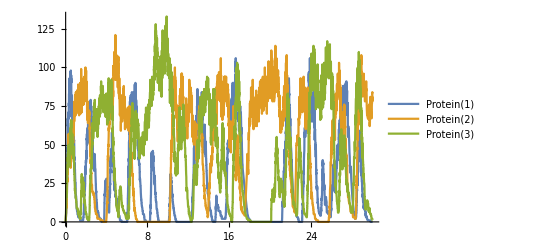

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
ListLinePlot[{trajlists[[Protein[1]/.species2numbers]],trajlists[[Protein[2]/.species2numbers]],trajlists[[Protein[3]/.species2numbers]]},PlotLegends->{Protein[1],Protein[2],Protein[3]}]]
```

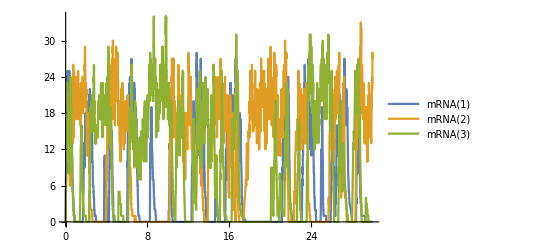

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
ListLinePlot[{trajlists[[mRNA[1]/.species2numbers]],trajlists[[mRNA[2]/.species2numbers]],trajlists[[mRNA[3]/.species2numbers]]},PlotLegends->{mRNA[1],mRNA[2],mRNA[3]}]]
```

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
With[{f1=Interpolation[trajlists[[Protein[1]/.species2numbers]],InterpolationOrder->1],
f2=Interpolation[trajlists[[Protein[2]/.species2numbers]],InterpolationOrder->1],
f3=Interpolation[trajlists[[Protein[3]/.species2numbers]],InterpolationOrder->1]},
ParametricPlot3D[{f1[t],f2[t],f3[t]}, {t,0,30},ColorFunction->Function[{x,y,z,t},Hue[t/30]],ColorFunctionScaling->False]]]
```

-Graphics3D-

So dimerization of repressors can be used to get a sigmoid that satisfies the digital abstraction, and can yield behaviors like oscillation -- but it must be tuned just right and it’s still quite noisy.

To get a sharper sigmoid with dimerized repressors, a cascade of NOT gates is required.  

There is an alternative mechanism for sigmoidal threshold behavior that easily obtains sharp IO curves with fewer genes:  titration of the input against a competitor being produced at a standard rate.  Here, we’ll number the competitors with negative indices.  Thus Protein[i] and Protein[-i] form an inert heterodimer -- only if Protein[i] is being produced faster, will there be a substantial amount left over to do the repression.

Conveniently, titration can be implemented via irreversible dimerization, so no new reaction schemata are needed.

To test a single NOT gate, we need to include the upstream gene (and not just upstream counts) because the mechanism relies on competition of production rates.

```mathematica
DefaultGRNratesWithDimers;
Timing[IO=Table[
initialstate=Genome[Promoter[-1],Gene[-1],Promoter[0],Gene[1],Promoter[1],Gene[2]] + 10000RNAP+50000Ribosome+1000RNase+500Protease;
Dimers={{-1,1}};
kbp[-1]=0; (* monomer form of protein -1 does not bind to its own promoter *)
ktx[1]=0.020; (* increase promoter strength to target average 20 mRNA thus average 100 protein when output is ON *)
ktx[-1]=0.010; (* the competitor protein is at half-max expression *)
ktx[0] = initialcount*0.020/100; (* we scan levels of expression for protein 1 *)
kbd[-1,1]=100; kud[-1,1]=0; (* heterodimer binding is super-fast and irreversible *)
kbp[1]=1; kup[1]=1; (* protein regulator binds tightly to promoter site; 1 repressor molecule gives half-max repression *)
{trajectory,species2numbers}=SimulateReactionSchemaSSA[GRNschemataDimers,initialstate,100,Trajectory->True];
PrintTemporary["Simulation for input protein count ",initialcount," completed."];
{initialcount, Mean[WeightedTrajectory[trajectory,Protein[2]/.species2numbers]]},
{initialcount,0,100,2}
];]  (* SSA is 1000x faster than the original *)
```

{193.083,Null}

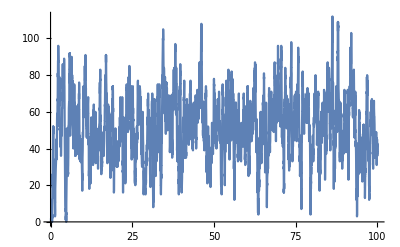
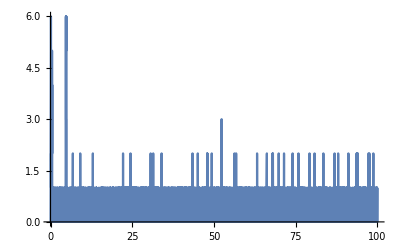
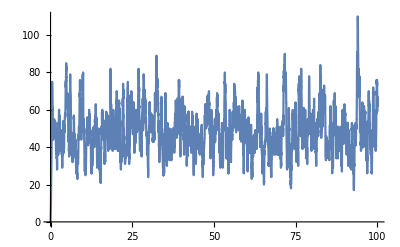
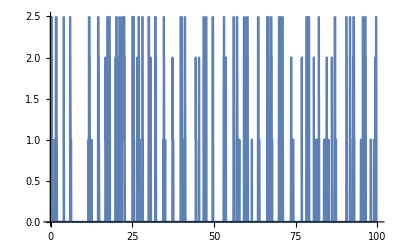
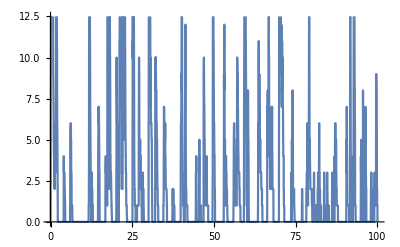

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
{ListLinePlot[trajlists[[Protein[1]/.species2numbers]]],ListLinePlot[trajlists[[Protein[-1]/.species2numbers]]],
ListLinePlot[trajlists[[Dimer[-1,1]/.species2numbers]]],
ListLinePlot[trajlists[[mRNA[2]/.species2numbers]]],ListLinePlot[trajlists[[Protein[2]/.species2numbers]]]}]
```

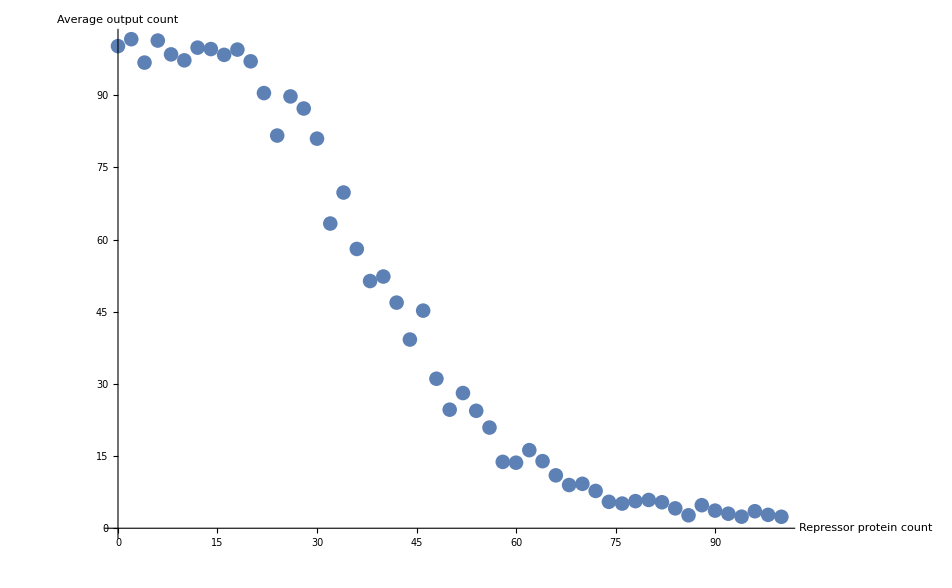

```mathematica
ListPlot[IO,AxesLabel->{"Repressor protein count","Average output count"},PlotRange->All]
```

In bulk, dimerizing repressors can achieve a Hill exponent of at most 2 (for a single-gene NOT gate), whereas competitive titration (for a single pair of genes) can achieve a Hill exponent of M where M is the ratio between the genome concentration and the ON signal level.   (Or can better be achieved?)  However, the stochastic version is not as crisp as bulk ODEs due to the fluctuations, but it’s still pretty darn good.  

And how good of an oscillator can we get from titration?  Six genes instead of three, but hey... it’s the best oscillator yet!

```mathematica
DefaultGRNratesWithDimers;
initialstate=Genome[Promoter[0],Gene[-1],Promoter[0],Gene[-2],Promoter[0],Gene[-3],Promoter[1],Gene[2],Promoter[2],Gene[3],Promoter[3],Gene[1]] + 10000RNAP+50000Ribosome+1000RNase+500Protease;
Dimers={{-1,1},{-2,2},{-3,3}}; (* repressors and their competitor form heterodimers *)
ktx[i_Integer]:=0.020; (* increase promoter strength to target average 20 mRNA thus average 100 protein when ON *)
ktx[0]=0.010; (* competitors express at half-max via promoter 0 *)
kbd[i_Integer,j_Integer]:=100; kud[i_Integer,j_Integer]:=0; (* heterodimer binding is super-fast and irreversible *)
kbp[i_Integer]:=1; kup[i_Integer]:=1; (* repressors bind strongly; 1 molecule is enough to significantly repress *)
(* note that to replace pattern-matching defaults, the same patterns must be used -- otherwise, Mathematica keeps both and which will match first depends on the order they are tried *)
```

```mathematica
Timing[{trajectory,species2numbers}=SimulateReactionSchemaSSA[GRNschemataDimers,initialstate,30,Trajectory->True];]
```

{4.03882,Null}

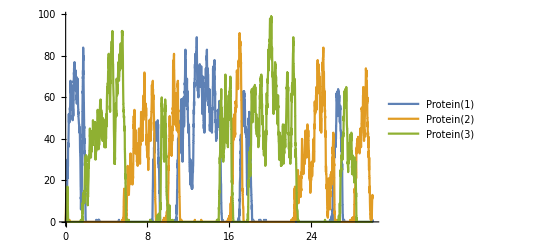

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
ListLinePlot[{trajlists[[Protein[1]/.species2numbers]],trajlists[[Protein[2]/.species2numbers]],trajlists[[Protein[3]/.species2numbers]]},PlotLegends->{Protein[1],Protein[2],Protein[3]}]]
```

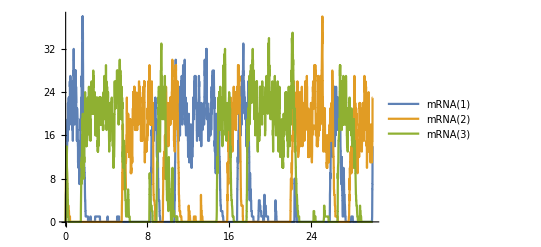

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
ListLinePlot[{trajlists[[mRNA[1]/.species2numbers]],trajlists[[mRNA[2]/.species2numbers]],trajlists[[mRNA[3]/.species2numbers]]},PlotLegends->{mRNA[1],mRNA[2],mRNA[3]}]]
```

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
With[{f1=Interpolation[trajlists[[Protein[1]/.species2numbers]],InterpolationOrder->1],
f2=Interpolation[trajlists[[Protein[2]/.species2numbers]],InterpolationOrder->1],
f3=Interpolation[trajlists[[Protein[3]/.species2numbers]],InterpolationOrder->1]},
ParametricPlot3D[{f1[t],f2[t],f3[t]}, {t,0,30},ColorFunction->Function[{x,y,z,t},Hue[t/30]],ColorFunctionScaling->False]]]
```

-Graphics3D-

Just for fun, note that using the CRN Simulator we can also perform a bulk ODE simulation of the same system.  Takes a while for numerical noise to break symmetry!  Neat!

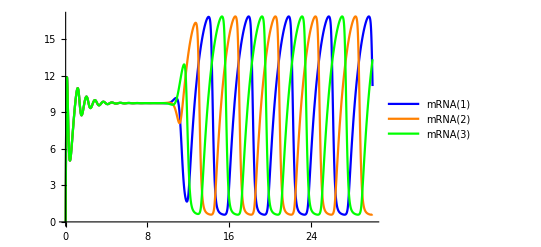

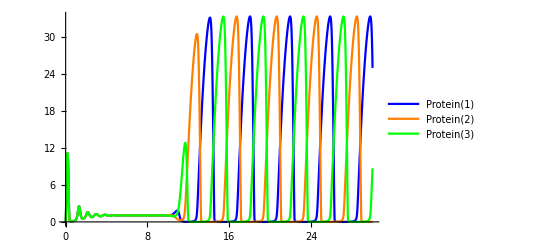

```mathematica
sol=SimulateReactionSchemaBulk[GRNschemataDimers,initialstate,30];
Plot[Evaluate[{mRNA[1][t],mRNA[2][t],mRNA[3][t]}/.sol],{t,0,30},PlotRange->{0,All},PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{mRNA[1],mRNA[2],mRNA[3]}]
Plot[Evaluate[{Protein[1][t],Protein[2][t],Protein[3][t]}/.sol],{t,0,30},PlotRange->{0,All},PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{Protein[1],Protein[2],Protein[3]}]
```

The competitive titration architecture is also especially good for building not only AND and OR and NOT gates, but more generally, n-input weighted neural network nodes.

## Cell-free PEN-DNA systems

Here we present reaction schemata for the PEN-DNA systems developed in Yannick Rondelez’s group.  We follow the model introduced in
	Montagne, Plasson, Sakai, Fujii, Rondelez, “Programming an in vitro DNA oscillator using a molecular networking strategy”, Molecular Systems Biology, 2011
	Padirac, Fujii, Rondelez, “Bottom-up construction of in vitro switchable memories”, PNAS, 2012

```mathematica
Clear[khyb,kdiss,kdissInh,kpol,kpolSD,kleak,knick,kexo];

PENDNAschemata = {
(* hybridization and dissociation of a single positive signal in either first or last position *)
rxnschema[Template[A_,a_,B_,b_]+Signal[A_,a_],Template[Signal[A,a],B,b],khyb],
rxnschema[Template[Signal[A_,a_],B_,b_],Template[A,a,B,b]+Signal[A,a],kdiss[A,a]],
rxnschema[Template[A_,a_,B_,b_]+Signal[B_,b_],Template[A,a,Signal[B,b]],khyb],
rxnschema[Template[A_,a_,Signal[B_,b_]],Template[A,a,B,b]+Signal[B,b],kdiss[B,b]],

(* hybridization and dissociation of positive signals involving two simultaneously bound to a template *)
rxnschema[Template[A_,a_,Signal[B_,b_]]+Signal[A_,a_],Template[Signal[A,a],Signal[B,b]],khyb],
rxnschema[Template[Signal[A_,a_],B_,b_]+Signal[B_,b_],Template[Signal[A,a],Signal[B,b]],khyb],
rxnschema[Template[Signal[A_,a_],Signal[B_,b_]],Template[Signal[A,a],B,b]+Signal[B,b],kdiss[B,b]],
rxnschema[Template[Signal[A_,a_],Signal[B_,b_]],Template[A,a,Signal[B,b]]+Signal[A,a],kdiss[A,a]],

(* hybridization and dissociation of inhibitory signals, and strand displacement of overlapping sites *)
rxnschema[Template[A_,a_,B_,b_]+Signal[a_,B_],Template[A,Signal[a,B],b],khyb],
rxnschema[Template[A_,Signal[a_,B_],b_],Template[A,a,B,b]+Signal[a,B],kdissInh[a,B]],
rxnschema[Template[Signal[A_,a_],B_,b_]+Signal[a_,B_],Template[A,Signal[a,B],b]+Signal[A,a],khyb],
rxnschema[Template[A_,a_,Signal[B_,b_]]+Signal[a_,B_],Template[A,Signal[a,B],b]+Signal[B,b],khyb],
rxnschema[Template[A_,Signal[a_,B_],b_]+Signal[A_,a_],Template[Signal[A,a],B,b]+Signal[a,B],khyb*kdissInh[a,B]/kdiss[A,a]],
rxnschema[Template[A_,Signal[a_,B_],b_]+Signal[B_,b_],Template[A,a,Signal[B,b]]+Signal[a,B],khyb*kdissInh[a,B]/kdiss[B,b]],

(* enzyme reactions *)
rxnschema[Template[Signal[A_,a_],B_,b_]+DNAPol,Template[Signal[A,a,B,b]]+DNAPol,kpol],
rxnschema[Template[A_,a_,B_,b_]+DNAPol,Template[A,a,Signal[B,b]]+DNAPol,kleak[B,b]],
rxnschema[Template[Signal[A_,a_],Signal[B_,b_]]+DNAPol,Template[Signal[A,a,B,b]]+Signal[B,b]+DNAPol,kpolSD[B,b]],
rxnschema[Template[Signal[A_,a_,B_,b_]]+Nickase,Template[Signal[A,a],Signal[B,b]]+Nickase,knick],
rxnschema[Signal[A_,a_]+Exonuclease,Exonuclease,kexo[A,a]]
};

(* these rate constants are ballpark estimates from the model in Rondelez 2011 *)
(* enzymes are supplied calibrated to "units", so default 100 nM concentrations are used here *)
DefaultPENDNArates:=Module[{},
Clear[khyb,kdiss,kdissInh,kpol,kpolSD,kleak,knick,kexo];
khyb=0.026; (* /nM/min *)
kdiss[_,_]:=1.6; (* /min *)   (* note that inhibitor species are usually longer, so use species-specific rules to decrease their kdiss *)
kdissInh[_,_]:=0.004; (* /min *)
kpol=0.17; (* /nM/min, corresponding to default being 100 nM enzyme *)
kpolSD[_,_]:=kpol;   (* might want to use species-specific rules to decrease this by x2 for inhibitor species *)
kleak[_,_]:=0.0001; (* /nM/min *)  (* this parameter was not in Rondelez; it's set to match Fig 1A *)
knick=0.03; (* /nM/min, corresponding to default being 100 nM enzyme *)
kexo[_,_]:=0.0063; (* /nM/min, corresponding to default being 100 nM enzyme *)
]
```

```mathematica
(* here we fill in the exact species-dependent rate constants used in the Rondelez 2011 model *)
DefaultPENDNArates
T1=Template[A,a,A,a];T2=Template[A,a,B,b];T3=Template[B,b,a,A];
D1=Template[Signal[A,a,A,a]];D2=Template[Signal[A,a,B,b]];D3=Template[Signal[B,b,a,A]];
SigA=Signal[A,a];SigB=Signal[B,b];Inh=Signal[a,A];
kdiss[A,a]=2.3;kdiss[B,b]=0.81;kdissInh[a,A]=0.0057;kdiss[a,A]=0.0021;
kpolSD[a,A]=0.069;kexo[A,a]=0.0032;kexo[B,b]=0.0037;kexo[a,A]=0.012;
experiment1A={60T1+100DNAPol+100Nickase,60T1+100DNAPol+100Nickase+100Exonuclease};
experiment1B=Table[60T1+100DNAPol+100Nickase+Round[frac 60] Inh,{frac,{0,0.15,0.5,0.65,0.8,1.0}}];
experiment1C={30T1+5T2+30T3+100DNAPol+100Nickase+100Exonuclease};
```

Reproducing the experiment from Figure 1A.  One difference: Rondelez initiated Fig 1A experiments with 0.1 nM SigA, whereas here instead we introduce kleak for DNAPol.  We don’t claim verisimilitude, but 0.1 nM is awkward for stochastic simulations tuned to 1.66 fL where a count of 1 molecules corresponds to 1 nM.  The same issue arises for Fig 1B.

```mathematica
EnumerateReactionSchema[PENDNAschemata,Last[experiment1A]]
```

{  Exonuclease+Signal[A,a]⟶^0.0032Exonuclease,  Nickase+Template[Signal[A,a,A,a]]⟶^0.03Nickase+Template[Signal[A,a],Signal[A,a]],  Template[Signal[A,a],Signal[A,a]]⟶^2.3Signal[A,a]+Template[A,a,Signal[A,a]],  Template[Signal[A,a],Signal[A,a]]⟶^2.3Signal[A,a]+Template[Signal[A,a],A,a],  DNAPol+Template[Signal[A,a],Signal[A,a]]⟶^0.17DNAPol+Signal[A,a]+Template[Signal[A,a,A,a]],  Template[A,a,Signal[A,a]]⟶^2.3Signal[A,a]+Template[A,a,A,a],  Signal[A,a]+Template[A,a,Signal[A,a]]⟶^0.026Template[Signal[A,a],Signal[A,a]],  Template[Signal[A,a],A,a]⟶^2.3Signal[A,a]+Template[A,a,A,a],  DNAPol+Template[Signal[A,a],A,a]⟶^0.17DNAPol+Template[Signal[A,a,A,a]],  Signal[A,a]+Template[Signal[A,a],A,a]⟶^0.026Template[Signal[A,a],Signal[A,a]],  DNAPol+Template[A,a,A,a]⟶^0.0001DNAPol+Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[Signal[A,a],A,a]}

```mathematica
Timing[
history1Aa=SimulateReactionSchemaSSA[PENDNAschemata,First[experiment1A],50];
history1Ab=SimulateReactionSchemaSSA[PENDNAschemata,Last[experiment1A],50];
Length/@{history1Aa,history1Ab}]
```

{16.1992,{16256,22119}}

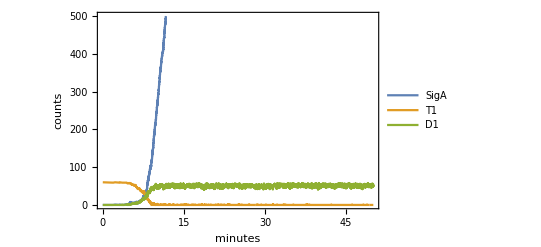
{-Graphics-,-Graphics-}

```mathematica
(* concentration of D1 may be best match to experimental measurement of fluorescence using a dye for double-stranded DNA *)
ListLinePlot[{DataTrace[#,SigA],DataTrace[#,T1],DataTrace[#,D1]},PlotRange->{{0,50},{0,500}},PlotLegends->{"SigA","T1","D1"},FrameLabel->{minutes,counts},Frame->True]&/@{history1Aa,history1Ab}
```

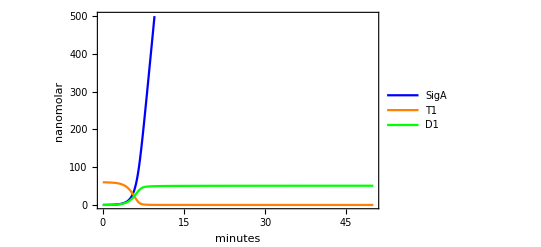
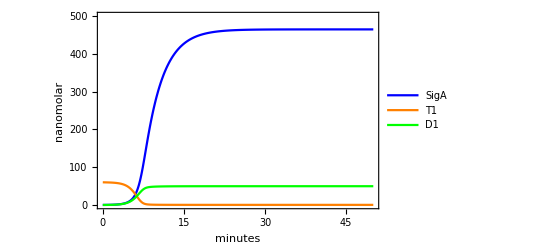

```mathematica
sol1Aa=SimulateReactionSchemaBulk[PENDNAschemata,First[experiment1A],50];
sol1Ab=SimulateReactionSchemaBulk[PENDNAschemata,Last[experiment1A],50];
Plot[Evaluate[{SigA[t],T1[t],D1[t]}/.#],{t,0,50},PlotRange->{{0,50},{0,500}},PlotStyle->{{Blue},{Orange},{Green}},PlotLegends->{"SigA","T1","D1"},FrameLabel->{minutes,nanomolar},Frame->True]&/@{sol1Aa,sol1Ab}
```

Reproducing the experiment from Figure 1B.   The simulations qualitatively match the experimental data, although for high initial inhibitor concentrations, the experimental fluorescence stays low for the first several minutes rather than increasing immediately.  Decreasing the amount of DNAPol by a factor of two provides a possibly better fit.

```mathematica
EnumerateReactionSchema[PENDNAschemata,Last[experiment1B]]
```

{  Nickase+Template[Signal[A,a,A,a]]⟶^0.03Nickase+Template[Signal[A,a],Signal[A,a]],  Template[Signal[A,a],Signal[A,a]]⟶^2.3Signal[A,a]+Template[A,a,Signal[A,a]],  Template[Signal[A,a],Signal[A,a]]⟶^2.3Signal[A,a]+Template[Signal[A,a],A,a],  DNAPol+Template[Signal[A,a],Signal[A,a]]⟶^0.17DNAPol+Signal[A,a]+Template[Signal[A,a,A,a]],  Template[A,a,Signal[A,a]]⟶^2.3Signal[A,a]+Template[A,a,A,a],  Signal[a,A]+Template[A,a,Signal[A,a]]⟶^0.026Signal[A,a]+Template[A,Signal[a,A],a],  Signal[A,a]+Template[A,a,Signal[A,a]]⟶^0.026Template[Signal[A,a],Signal[A,a]],  Template[A,Signal[a,A],a]⟶^0.0057Signal[a,A]+Template[A,a,A,a],  Signal[A,a]+Template[A,Signal[a,A],a]⟶^0.0000644348Signal[a,A]+Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,Signal[a,A],a]⟶^0.0000644348Signal[a,A]+Template[Signal[A,a],A,a],  Template[Signal[A,a],A,a]⟶^2.3Signal[A,a]+Template[A,a,A,a],  DNAPol+Template[Signal[A,a],A,a]⟶^0.17DNAPol+Template[Signal[A,a,A,a]],  Signal[a,A]+Template[Signal[A,a],A,a]⟶^0.026Signal[A,a]+Template[A,Signal[a,A],a],  Signal[A,a]+Template[Signal[A,a],A,a]⟶^0.026Template[Signal[A,a],Signal[A,a]],  DNAPol+Template[A,a,A,a]⟶^0.0001DNAPol+Template[A,a,Signal[A,a]],  Signal[a,A]+Template[A,a,A,a]⟶^0.026Template[A,Signal[a,A],a],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[Signal[A,a],A,a]}

```mathematica
Timing[
history=Table[SimulateReactionSchemaSSA[PENDNAschemata,exp,80],{exp,experiment1B}];
Length/@history]
```

{73.7876,{25718,27205,26002,22403,21411,17684}}

```mathematica
ListLinePlot[Table[DataTrace[history[[i]],D1],{i,1,6}],PlotRange->{{0,80},{0,75}},PlotLabel->"Fully duplex template",PlotLegends->Table["Inh = " <>ToString[f]<>" T1",{f,{0,0.15,0.5,0.65,0.8,1.0}}],FrameLabel->{minutes,counts},Frame->True]
```

-Graphics-

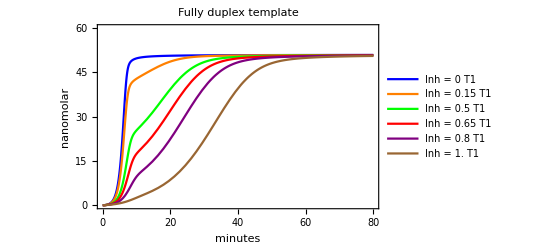

```mathematica
sols=Table[SimulateReactionSchemaBulk[PENDNAschemata,exp-0 DNAPol,80],{exp,experiment1B}];
Plot[Evaluate[Table[D1[t]/.sol,{sol,sols}]],{t,0,80},PlotRange->{{0,80},{0,60}},PlotStyle->{{Blue},{Orange},{Green},{Red},{Purple},{Brown}},PlotLegends->Table["Inh = " <>ToString[f]<>" T1",{f,{0,0.15,0.5,0.65,0.8,1.0}}],FrameLabel->{minutes,nanomolar},Frame->True,PlotLabel->"Fully duplex template"]
```

Reproducing the experiment from Figure 1C.   Using the initial parameters, we get strongly damped oscillations, in contrast to the experimental data and the model in the paper.  It is not clear what change between the model there and the one here that accounts for the difference.   By changing the simulated enzyme concentrations (equivalent to changing their rate constants, since they are modeled as first-order catalytic reactions) and template concentrations, oscillations are recovered.

```mathematica
EnumerateReactionSchema[PENDNAschemata,First[experiment1C]]
```

{  Exonuclease+Signal[a,A]⟶^0.012Exonuclease,  Exonuclease+Signal[A,a]⟶^0.0032Exonuclease,  Exonuclease+Signal[B,b]⟶^0.0037Exonuclease,  Nickase+Template[Signal[A,a,A,a]]⟶^0.03Nickase+Template[Signal[A,a],Signal[A,a]],  Nickase+Template[Signal[A,a,B,b]]⟶^0.03Nickase+Template[Signal[A,a],Signal[B,b]],  Nickase+Template[Signal[B,b,a,A]]⟶^0.03Nickase+Template[Signal[B,b],Signal[a,A]],  Template[Signal[A,a],Signal[A,a]]⟶^2.3Signal[A,a]+Template[A,a,Signal[A,a]],  Template[Signal[A,a],Signal[A,a]]⟶^2.3Signal[A,a]+Template[Signal[A,a],A,a],  DNAPol+Template[Signal[A,a],Signal[A,a]]⟶^0.17DNAPol+Signal[A,a]+Template[Signal[A,a,A,a]],  Template[Signal[A,a],Signal[B,b]]⟶^2.3Signal[A,a]+Template[A,a,Signal[B,b]],  Template[Signal[A,a],Signal[B,b]]⟶^0.81Signal[B,b]+Template[Signal[A,a],B,b],  DNAPol+Template[Signal[A,a],Signal[B,b]]⟶^0.17DNAPol+Signal[B,b]+Template[Signal[A,a,B,b]],  Template[Signal[B,b],Signal[a,A]]⟶^0.81Signal[B,b]+Template[B,b,Signal[a,A]],  Template[Signal[B,b],Signal[a,A]]⟶^0.0021Signal[a,A]+Template[Signal[B,b],a,A],  DNAPol+Template[Signal[B,b],Signal[a,A]]⟶^0.069DNAPol+Signal[a,A]+Template[Signal[B,b,a,A]],  Template[A,a,Signal[A,a]]⟶^2.3Signal[A,a]+Template[A,a,A,a],  Signal[a,A]+Template[A,a,Signal[A,a]]⟶^0.026Signal[A,a]+Template[A,Signal[a,A],a],  Signal[A,a]+Template[A,a,Signal[A,a]]⟶^0.026Template[Signal[A,a],Signal[A,a]],  Template[A,a,Signal[B,b]]⟶^0.81Signal[B,b]+Template[A,a,B,b],  Signal[A,a]+Template[A,a,Signal[B,b]]⟶^0.026Template[Signal[A,a],Signal[B,b]],  Template[A,Signal[a,A],a]⟶^0.0057Signal[a,A]+Template[A,a,A,a],  Signal[A,a]+Template[A,Signal[a,A],a]⟶^0.0000644348Signal[a,A]+Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,Signal[a,A],a]⟶^0.0000644348Signal[a,A]+Template[Signal[A,a],A,a],  Template[B,b,Signal[a,A]]⟶^0.0021Signal[a,A]+Template[B,b,a,A],  Signal[B,b]+Template[B,b,Signal[a,A]]⟶^0.026Template[Signal[B,b],Signal[a,A]],  Template[Signal[A,a],A,a]⟶^2.3Signal[A,a]+Template[A,a,A,a],  DNAPol+Template[Signal[A,a],A,a]⟶^0.17DNAPol+Template[Signal[A,a,A,a]],  Signal[a,A]+Template[Signal[A,a],A,a]⟶^0.026Signal[A,a]+Template[A,Signal[a,A],a],  Signal[A,a]+Template[Signal[A,a],A,a]⟶^0.026Template[Signal[A,a],Signal[A,a]],  Template[Signal[A,a],B,b]⟶^2.3Signal[A,a]+Template[A,a,B,b],  DNAPol+Template[Signal[A,a],B,b]⟶^0.17DNAPol+Template[Signal[A,a,B,b]],  Signal[B,b]+Template[Signal[A,a],B,b]⟶^0.026Template[Signal[A,a],Signal[B,b]],  Template[Signal[B,b],a,A]⟶^0.81Signal[B,b]+Template[B,b,a,A],  DNAPol+Template[Signal[B,b],a,A]⟶^0.17DNAPol+Template[Signal[B,b,a,A]],  Signal[a,A]+Template[Signal[B,b],a,A]⟶^0.026Template[Signal[B,b],Signal[a,A]],  DNAPol+Template[A,a,A,a]⟶^0.0001DNAPol+Template[A,a,Signal[A,a]],  Signal[a,A]+Template[A,a,A,a]⟶^0.026Template[A,Signal[a,A],a],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[Signal[A,a],A,a],  DNAPol+Template[A,a,B,b]⟶^0.0001DNAPol+Template[A,a,Signal[B,b]],  Signal[A,a]+Template[A,a,B,b]⟶^0.026Template[Signal[A,a],B,b],  Signal[B,b]+Template[A,a,B,b]⟶^0.026Template[A,a,Signal[B,b]],  DNAPol+Template[B,b,a,A]⟶^0.0001DNAPol+Template[B,b,Signal[a,A]],  Signal[a,A]+Template[B,b,a,A]⟶^0.026Template[B,b,Signal[a,A]],  Signal[B,b]+Template[B,b,a,A]⟶^0.026Template[Signal[B,b],a,A]}

```mathematica
sol=SimulateReactionSchemaBulk[PENDNAschemata,First[experiment1C],1800];
Plot[Evaluate[{T1[t],T2[t],T3[t],SigA[t],SigB[t],Inh[t]}/.sol],{t,0,1800},PlotRange->{{0,1800},{0,30}},PlotLegends->{"T1","T2","T3","SigA","SigB","Inh"},FrameLabel->{minutes,nanomolar},Frame->True]
```

-Graphics-

```mathematica
sol=SimulateReactionSchemaBulk[PENDNAschemata,First[experiment1C]+30T1+30T3-3T2-20Exonuclease-75DNAPol,1800];
Plot[Evaluate[{T1[t],T2[t],T3[t],SigA[t],SigB[t],Inh[t]}/.sol],{t,0,1800},PlotRange->{{0,1800},{0,30}},PlotLegends->{"T1","T2","T3","SigA","SigB","Inh"},FrameLabel->{minutes,nanomolar},Frame->True]
```

-Graphics-

```mathematica
Timing[{trajectory,species2numbers}=SimulateReactionSchemaSSA[PENDNAschemata,First[experiment1C]+30T1+30T3-3T2-20Exonuclease-75DNAPol,1800,Trajectory->True]; Length[trajectory["Values"]]]
```

{2.16561,60113}

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
ListLinePlot[{
trajlists[[SigA/.species2numbers]],
trajlists[[SigB/.species2numbers]],
trajlists[[Inh/.species2numbers]]
},PlotLegends->{"SigA","SigB","Inh"},PlotRange->All]]
```

-Graphics-

```mathematica
With[{trajlists=PlotFormat[trajectory,5000]},
ListLinePlot[{
trajlists[[T1/.species2numbers]],
trajlists[[T2/.species2numbers]],
trajlists[[T3/.species2numbers]]
},PlotLegends->{"T1","T2","T3"},PlotRange->All]]
```

-Graphics-

Moving on the 2012 paper and bistable memories.  Here, we don’t try to reproduce the idiosyncrasies of each template, and just use generic (and symmetric) parameters; therefore we also don’t attempt to reproduce the exact experiments, but rather demonstrate them in spirit.  We just demonstrate the simple bistable circuit.  It is interesting that while the bulk CRN behaves beautifully, the stochastic CRN (in the chosen volume) is quite unreliable unless the initial counts are substantially different.

```mathematica
DefaultPENDNArates
Ta2a=Template[A,a,A,a];Ta2ib=Template[A,a,b,B];Tb2b=Template[B,b,B,b]; Tb2ia=Template[B,b,a,A];
SigA=Signal[A,a];SigB=Signal[B,b];InhA=Signal[a,A]; InhB=Signal[b,B];
kdissInh[a,A]=0.006;kdiss[a,A]=0.002;kdissInh[b,B]=0.006;kdiss[b,B]=0.002;
kpolSD[a,A]=0.07;kpolSD[b,B]=0.07;kexo[A,a]=0.003;kexo[B,b]=0.003;kexo[a,A]=0.01; kexo[b,B]=0.01;
stock=20Ta2a+20Ta2ib+20Tb2b+20Tb2ia+100DNAPol+100Nickase+100Exonuclease;
experiment3BC={SigB,SigA,20SigA+60SigB,60SigA+20SigB}+stock;
experiment3DE=Table[n SigA+m SigB+stock,{n,{1,2,4,8,16,32}},{m,{1,2,4,8,16,32}}];
```

```mathematica
EnumerateReactionSchema[PENDNAschemata,Last[experiment3BC]]
```

{  Exonuclease+Signal[a,A]⟶^0.01Exonuclease,  Exonuclease+Signal[A,a]⟶^0.003Exonuclease,  Exonuclease+Signal[b,B]⟶^0.01Exonuclease,  Exonuclease+Signal[B,b]⟶^0.003Exonuclease,  Nickase+Template[Signal[A,a,A,a]]⟶^0.03Nickase+Template[Signal[A,a],Signal[A,a]],  Nickase+Template[Signal[A,a,b,B]]⟶^0.03Nickase+Template[Signal[A,a],Signal[b,B]],  Nickase+Template[Signal[B,b,a,A]]⟶^0.03Nickase+Template[Signal[B,b],Signal[a,A]],  Nickase+Template[Signal[B,b,B,b]]⟶^0.03Nickase+Template[Signal[B,b],Signal[B,b]],  Template[Signal[A,a],Signal[A,a]]⟶^1.6Signal[A,a]+Template[A,a,Signal[A,a]],  Template[Signal[A,a],Signal[A,a]]⟶^1.6Signal[A,a]+Template[Signal[A,a],A,a],  DNAPol+Template[Signal[A,a],Signal[A,a]]⟶^0.17DNAPol+Signal[A,a]+Template[Signal[A,a,A,a]],  Template[Signal[A,a],Signal[b,B]]⟶^1.6Signal[A,a]+Template[A,a,Signal[b,B]],  Template[Signal[A,a],Signal[b,B]]⟶^0.002Signal[b,B]+Template[Signal[A,a],b,B],  DNAPol+Template[Signal[A,a],Signal[b,B]]⟶^0.07DNAPol+Signal[b,B]+Template[Signal[A,a,b,B]],  Template[Signal[B,b],Signal[a,A]]⟶^1.6Signal[B,b]+Template[B,b,Signal[a,A]],  Template[Signal[B,b],Signal[a,A]]⟶^0.002Signal[a,A]+Template[Signal[B,b],a,A],  DNAPol+Template[Signal[B,b],Signal[a,A]]⟶^0.07DNAPol+Signal[a,A]+Template[Signal[B,b,a,A]],  Template[Signal[B,b],Signal[B,b]]⟶^1.6Signal[B,b]+Template[B,b,Signal[B,b]],  Template[Signal[B,b],Signal[B,b]]⟶^1.6Signal[B,b]+Template[Signal[B,b],B,b],  DNAPol+Template[Signal[B,b],Signal[B,b]]⟶^0.17DNAPol+Signal[B,b]+Template[Signal[B,b,B,b]],  Template[A,a,Signal[A,a]]⟶^1.6Signal[A,a]+Template[A,a,A,a],  Signal[a,A]+Template[A,a,Signal[A,a]]⟶^0.026Signal[A,a]+Template[A,Signal[a,A],a],  Signal[A,a]+Template[A,a,Signal[A,a]]⟶^0.026Template[Signal[A,a],Signal[A,a]],  Template[A,a,Signal[b,B]]⟶^0.002Signal[b,B]+Template[A,a,b,B],  Signal[A,a]+Template[A,a,Signal[b,B]]⟶^0.026Template[Signal[A,a],Signal[b,B]],  Template[A,Signal[a,A],a]⟶^0.006Signal[a,A]+Template[A,a,A,a],  Signal[A,a]+Template[A,Signal[a,A],a]⟶^0.0000975Signal[a,A]+Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,Signal[a,A],a]⟶^0.0000975Signal[a,A]+Template[Signal[A,a],A,a],  Template[B,b,Signal[a,A]]⟶^0.002Signal[a,A]+Template[B,b,a,A],  Signal[B,b]+Template[B,b,Signal[a,A]]⟶^0.026Template[Signal[B,b],Signal[a,A]],  Template[B,b,Signal[B,b]]⟶^1.6Signal[B,b]+Template[B,b,B,b],  Signal[b,B]+Template[B,b,Signal[B,b]]⟶^0.026Signal[B,b]+Template[B,Signal[b,B],b],  Signal[B,b]+Template[B,b,Signal[B,b]]⟶^0.026Template[Signal[B,b],Signal[B,b]],  Template[B,Signal[b,B],b]⟶^0.006Signal[b,B]+Template[B,b,B,b],  Signal[B,b]+Template[B,Signal[b,B],b]⟶^0.0000975Signal[b,B]+Template[B,b,Signal[B,b]],  Signal[B,b]+Template[B,Signal[b,B],b]⟶^0.0000975Signal[b,B]+Template[Signal[B,b],B,b],  Template[Signal[A,a],A,a]⟶^1.6Signal[A,a]+Template[A,a,A,a],  DNAPol+Template[Signal[A,a],A,a]⟶^0.17DNAPol+Template[Signal[A,a,A,a]],  Signal[a,A]+Template[Signal[A,a],A,a]⟶^0.026Signal[A,a]+Template[A,Signal[a,A],a],  Signal[A,a]+Template[Signal[A,a],A,a]⟶^0.026Template[Signal[A,a],Signal[A,a]],  Template[Signal[A,a],b,B]⟶^1.6Signal[A,a]+Template[A,a,b,B],  DNAPol+Template[Signal[A,a],b,B]⟶^0.17DNAPol+Template[Signal[A,a,b,B]],  Signal[b,B]+Template[Signal[A,a],b,B]⟶^0.026Template[Signal[A,a],Signal[b,B]],  Template[Signal[B,b],a,A]⟶^1.6Signal[B,b]+Template[B,b,a,A],  DNAPol+Template[Signal[B,b],a,A]⟶^0.17DNAPol+Template[Signal[B,b,a,A]],  Signal[a,A]+Template[Signal[B,b],a,A]⟶^0.026Template[Signal[B,b],Signal[a,A]],  Template[Signal[B,b],B,b]⟶^1.6Signal[B,b]+Template[B,b,B,b],  DNAPol+Template[Signal[B,b],B,b]⟶^0.17DNAPol+Template[Signal[B,b,B,b]],  Signal[b,B]+Template[Signal[B,b],B,b]⟶^0.026Signal[B,b]+Template[B,Signal[b,B],b],  Signal[B,b]+Template[Signal[B,b],B,b]⟶^0.026Template[Signal[B,b],Signal[B,b]],  DNAPol+Template[A,a,A,a]⟶^0.0001DNAPol+Template[A,a,Signal[A,a]],  Signal[a,A]+Template[A,a,A,a]⟶^0.026Template[A,Signal[a,A],a],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[A,a,Signal[A,a]],  Signal[A,a]+Template[A,a,A,a]⟶^0.026Template[Signal[A,a],A,a],  DNAPol+Template[A,a,b,B]⟶^0.0001DNAPol+Template[A,a,Signal[b,B]],  Signal[A,a]+Template[A,a,b,B]⟶^0.026Template[Signal[A,a],b,B],  Signal[b,B]+Template[A,a,b,B]⟶^0.026Template[A,a,Signal[b,B]],  DNAPol+Template[B,b,a,A]⟶^0.0001DNAPol+Template[B,b,Signal[a,A]],  Signal[a,A]+Template[B,b,a,A]⟶^0.026Template[B,b,Signal[a,A]],  Signal[B,b]+Template[B,b,a,A]⟶^0.026Template[Signal[B,b],a,A],  DNAPol+Template[B,b,B,b]⟶^0.0001DNAPol+Template[B,b,Signal[B,b]],  Signal[b,B]+Template[B,b,B,b]⟶^0.026Template[B,Signal[b,B],b],  Signal[B,b]+Template[B,b,B,b]⟶^0.026Template[B,b,Signal[B,b]],  Signal[B,b]+Template[B,b,B,b]⟶^0.026Template[Signal[B,b],B,b]}

```mathematica
Table[
{trajectory,species2numbers}=SimulateReactionSchemaSSA[PENDNAschemata,exp,200,Trajectory->True];
With[{trajlists=PlotFormat[trajectory,5000]},
ListLinePlot[{trajlists[[SigA/.species2numbers]],trajlists[[SigB/.species2numbers]]},PlotLegends->{"SigA","SigB"},PlotRange->All]],
{exp,experiment3BC}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

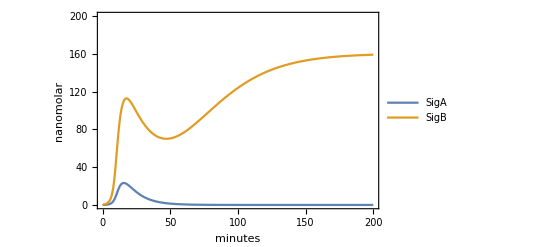
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sols=SimulateReactionSchemaBulk[PENDNAschemata,#,200]&/@experiment3BC;
Table[
Plot[Evaluate[{SigA[t],SigB[t]}/.sol],{t,0,200},PlotRange->{{0,200},{0,200}},PlotLegends->{"SigA","SigB"},FrameLabel->{minutes,nanomolar},Frame->True],
{sol,sols}]
```

```mathematica
Table[Show[
ParametricPlot[Evaluate[{SigA[t],SigB[t]}/.sol],{t,0,200},PlotRange->{{0,200},{0,200}},FrameLabel->{"SigA (nM)","SigB (nM)"},Frame->True],
Graphics[{If[(SigB[200]/.sol)>(SigA[200]/.sol),Red,Blue],Disk[{SigA[200],SigB[200]}/.sol,10]}]
],{sol,sols}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[Function[{exp},
sol=SimulateReactionSchemaBulk[PENDNAschemata,exp,200];
Show[
ParametricPlot[Evaluate[{SigA[t],SigB[t]}/.sol],{t,0,200},PlotRange->{{0,200},{0,200}},FrameLabel->{"SigA (nM)","SigB (nM)"},Frame->True],
Graphics[{If[(SigB[200]/.sol)>(SigA[200]/.sol),Red,Blue],Disk[{SigA[200],SigB[200]}/.sol,10]}]
]],
experiment3DE,{2}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

### Some relevant references

Elowitz, Michael B., and Stanislas Leibler. “A synthetic oscillatory network of transcriptional regulators.” Nature 403, no. 6767 (2000): 335-338.
Cuba Samaniego, Christian, Giulia Giordano, Jongmin Kim, Franco Blanchini, and Elisa Franco. “Molecular titration promotes oscillations and bistability in minimal network models with monomeric regulators.” ACS synthetic biology 5, no. 4 (2016): 321-333.
Montagne, Kevin, Raphael Plasson, Yasuyuki Sakai, Teruo Fujii, and Yannick Rondelez. “Programming an in vitro DNA oscillator using a molecular networking strategy.” Molecular systems biology 7, no. 1 (2011): 466.
Padirac, Adrien, Teruo Fujii, and Yannick Rondelez. “Bottom-up construction of in vitro switchable memories.” Proceedings of the National Academy of Sciences 109, no. 47 (2012): E3212-E3220.